```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[m],Join[Table[{i,i-1},{i,Range[2,m,1]}],Table[{i,i+1},{i,Range[1,m,1]}]]->-t]
```

```mathematica
T[t_,m_]:=T[t,m]=t*IdentityMatrix[m]
```

```mathematica
Clear[LEFT]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_,m_]:=LEFT[ω,δ,t,ϵ,m]=lead[[ω*100+1]]
```

```mathematica
g[ω_,δ_,t_,ϵ_,m_]:= Inverse[β[ω,δ,t,ϵ,m]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-g[ω,δ,t,ϵ,m].T[t,m].LEFT[ω,δ,t,ϵ,m].T[t,m]].g[ω,δ,t,ϵ,m]
```

```mathematica
SL[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-g[ω,δ,t,ϵ,m].T[t,m].LEFT[ω,δ,t,ϵ,m].T[t,m]].g[ω,δ,t,ϵ,m]
```

```mathematica
tr[0,0.0001,1,0,2]
```

tr[0,0.0001,1,0,2]

```mathematica
IL[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-SL[ω,δ,t,ϵ,m].T[t,m].SR[ω,δ,t,ϵ,m].T[t,m]].SL[ω,δ,t,ϵ,m]
```

```mathematica
IR[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-SR[ω,δ,t,ϵ,m].T[t,m].SL[ω,δ,t,ϵ,m].T[t,m]].SR[ω,δ,t,ϵ,m]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_,m_]:= IL[ω,δ,t,ϵ,m]-ConjugateTranspose[IL[ω,δ,t,ϵ,m]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_,m_]:= IR[ω,δ,t,ϵ,m]-ConjugateTranspose[IR[ω,δ,t,ϵ,m]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_,m_]:= SR[ω,δ,t,ϵ,m].T[t,m].IL[ω,δ,t,ϵ,m]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_,m_]:= Gnonlocal[ω,δ,t,ϵ,m]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ,m]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_,m_]:= Abs[Tr[gdd[ω,δ,t,ϵ,m].T[t,m].grr[ω,δ,t,ϵ,m].T[t,m]-T[t,m].GNON[ω,δ,t,ϵ,m].T[t,m].GNON[ω,δ,t,ϵ,m]]]
```

```mathematica
Do[Export["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/lead_new/L_"<>ToString[ω]<>".dat",SR[ω,0.0001,1,0,20]],{ω,Range[0,4,0.01]}]
```

```mathematica
lead=Table[ToExpression[Import["/home/shardulmukim/PhD/fwi/sq_lattice/20sq/lead_new/L_"<>ToString[ω]<>".dat"]],{ω,Range[0,4,0.01]}]
```

{1}
 |  |  |  |

```mathematica
pris=Table[{ω,Abs[tr[ω,0.0001,1,0,20]]},{ω,Range[0,4,0.01]}]
```

{{0.,20.},{0.01,20.},{0.02,19.9995},{0.03,19.},{0.04,19.},{0.05,19.},{0.06,19.},{0.07,19.},{0.08,19.},{0.09,18.0019},{0.1,18.},{0.11,18.},{0.12,18.},{0.13,18.},{0.14,18.},{0.15,18.},{0.16,18.},{0.17,18.},{0.18,18.},{0.19,18.},{0.2,17.0007},{0.21,17.},{0.22,17.},{0.23,17.},{0.24,17.},{0.25,17.},{0.26,17.},{0.27,17.},{0.28,17.},{0.29,17.},{0.3,17.},{0.31,17.},{0.32,17.},{0.33,17.},{0.34,17.},{0.35,16.0004},{0.36,16.},{0.37,16.},{0.38,16.},{0.39,16.},{0.4,16.},{0.41,16.},{0.42,16.},{0.43,16.},{0.44,16.},{0.45,16.},{0.46,16.},{0.47,16.},{0.48,16.},{0.49,16.},{0.5,16.},{0.51,16.},{0.52,16.},{0.53,15.9998},{0.54,15.0001},{0.55,15.},{0.56,15.},{0.57,15.},{0.58,15.},{0.59,15.},{0.6,15.},{0.61,15.},{0.62,15.},{0.63,15.},{0.64,15.},{0.65,15.},{0.66,15.},{0.67,15.},{0.68,15.},{0.69,15.},{0.7,15.},{0.71,15.},{0.72,15.},{0.73,15.},{0.74,15.},{0.75,14.9997},{0.76,14.0001},{0.77,14.},{0.78,14.},{0.79,14.},{0.8,14.},{0.81,14.},{0.82,14.},{0.83,14.},{0.84,14.},{0.85,14.},{0.86,14.},{0.87,14.},{0.88,14.},{0.89,14.},{0.9,14.},{0.91,14.},{0.92,14.},{0.93,14.},{0.94,14.},{0.95,14.},{0.96,14.},{0.97,14.},{0.98,14.},{0.99,14.},{1.,13.5},{1.01,13.},{1.02,13.},{1.03,13.},{1.04,13.},{1.05,13.},{1.06,13.},{1.07,13.},{1.08,13.},{1.09,13.},{1.1,13.},{1.11,13.},{1.12,13.},{1.13,13.},{1.14,13.},{1.15,13.},{1.16,13.},{1.17,13.},{1.18,13.},{1.19,13.},{1.2,13.},{1.21,13.},{1.22,13.},{1.23,13.},{1.24,13.},{1.25,13.},{1.26,13.},{1.27,12.0053},{1.28,12.},{1.29,12.},{1.3,12.},{1.31,12.},{1.32,12.},{1.33,12.},{1.34,12.},{1.35,12.},{1.36,12.},{1.37,12.},{1.38,12.},{1.39,12.},{1.4,12.},{1.41,12.},{1.42,12.},{1.43,12.},{1.44,12.},{1.45,12.},{1.46,12.},{1.47,12.},{1.48,12.},{1.49,12.},{1.5,12.},{1.51,12.},{1.52,12.},{1.53,12.},{1.54,12.},{1.55,11.9999},{1.56,11.0001},{1.57,11.},{1.58,11.},{1.59,11.},{1.6,11.},{1.61,11.},{1.62,11.},{1.63,11.},{1.64,11.},{1.65,11.},{1.66,11.},{1.67,11.},{1.68,11.},{1.69,11.},{1.7,11.},{1.71,11.},{1.72,11.},{1.73,11.},{1.74,11.},{1.75,11.},{1.76,11.},{1.77,11.},{1.78,11.},{1.79,11.},{1.8,11.},{1.81,11.},{1.82,11.},{1.83,11.},{1.84,11.},{1.85,10.9916},{1.86,10.},{1.87,10.},{1.88,10.},{1.89,10.},{1.9,10.},{1.91,10.},{1.92,10.},{1.93,10.},{1.94,10.},{1.95,10.},{1.96,10.},{1.97,10.},{1.98,10.},{1.99,10.},{2.,10.},{2.01,10.},{2.02,10.},{2.03,10.},{2.04,10.},{2.05,10.},{2.06,10.},{2.07,10.},{2.08,10.},{2.09,10.},{2.1,10.},{2.11,10.},{2.12,10.},{2.13,9.99999},{2.14,9.99997},{2.15,9.00836},{2.16,9.00002},{2.17,9.00001},{2.18,9.},{2.19,9.},{2.2,9.},{2.21,9.},{2.22,9.},{2.23,9.},{2.24,9.},{2.25,9.},{2.26,9.},{2.27,9.},{2.28,9.},{2.29,9.},{2.3,9.},{2.31,9.},{2.32,9.},{2.33,9.},{2.34,9.},{2.35,9.},{2.36,9.},{2.37,9.},{2.38,9.},{2.39,9.},{2.4,9.},{2.41,9.},{2.42,9.},{2.43,8.99999},{2.44,8.9999},{2.45,8.0001},{2.46,8.00001},{2.47,8.},{2.48,8.},{2.49,8.},{2.5,8.},{2.51,8.},{2.52,8.},{2.53,8.},{2.54,8.},{2.55,8.},{2.56,8.},{2.57,8.},{2.58,8.},{2.59,8.},{2.6,8.},{2.61,8.},{2.62,8.},{2.63,8.},{2.64,8.},{2.65,8.},{2.66,8.},{2.67,8.},{2.68,8.},{2.69,8.},{2.7,8.},{2.71,7.99999},{2.72,7.99998},{2.73,7.99471},{2.74,7.00003},{2.75,7.00001},{2.76,7.},{2.77,7.},{2.78,7.},{2.79,7.},{2.8,7.},{2.81,7.},{2.82,7.},{2.83,7.},{2.84,7.},{2.85,7.},{2.86,7.},{2.87,7.},{2.88,7.},{2.89,7.},{2.9,7.},{2.91,7.},{2.92,7.},{2.93,7.},{2.94,7.},{2.95,7.},{2.96,7.},{2.97,7.},{2.98,6.99999},{2.99,6.99997},{3.,6.49999},{3.01,6.00002},{3.02,6.00001},{3.03,6.},{3.04,6.},{3.05,6.},{3.06,6.},{3.07,6.},{3.08,6.},{3.09,6.},{3.1,6.},{3.11,6.},{3.12,6.},{3.13,6.},{3.14,6.},{3.15,6.},{3.16,6.},{3.17,6.},{3.18,6.},{3.19,6.},{3.2,6.},{3.21,6.},{3.22,6.},{3.23,5.99999},{3.24,5.99995},{3.25,5.00027},{3.26,5.00001},{3.27,5.},{3.28,5.},{3.29,5.},{3.3,5.},{3.31,5.},{3.32,5.},{3.33,5.},{3.34,5.},{3.35,5.},{3.36,5.},{3.37,5.},{3.38,5.},{3.39,5.},{3.4,5.},{3.41,5.},{3.42,5.},{3.43,5.},{3.44,5.},{3.45,4.99999},{3.46,4.99993},{3.47,4.00016},{3.48,4.00001},{3.49,4.},{3.5,4.},{3.51,4.},{3.52,4.},{3.53,4.},{3.54,4.},{3.55,4.},{3.56,4.},{3.57,4.},{3.58,4.},{3.59,4.},{3.6,4.},{3.61,4.},{3.62,4.},{3.63,3.99999},{3.64,3.99998},{3.65,3.99959},{3.66,3.00004},{3.67,3.00001},{3.68,3.},{3.69,3.},{3.7,3.},{3.71,3.},{3.72,3.},{3.73,3.},{3.74,3.},{3.75,3.},{3.76,3.},{3.77,3.},{3.78,2.99999},{3.79,2.99998},{3.8,2.99933},{3.81,2.00004},{3.82,2.00001},{3.83,2.},{3.84,2.},{3.85,2.},{3.86,2.},{3.87,2.},{3.88,2.},{3.89,1.99999},{3.9,1.99998},{3.91,1.9981},{3.92,1.00003},{3.93,1.00001},{3.94,1.},{3.95,0.999998},{3.96,0.999993},{3.97,0.999958},{3.98,0.000456674},{3.99,0.0000168049},{4.,5.34708×10^-6}}

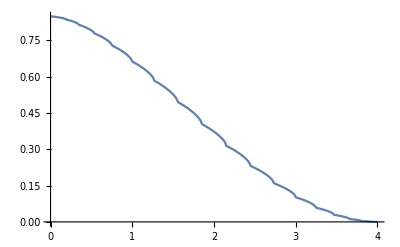

```mathematica
ListLinePlot[Table[{ω,-Im[SL[ω,0.0001,1,0,20][[1,1]]]},{ω,Range[0,4,0.01]}]]
```

```mathematica
Clear[imp,imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14,imp,list,b,surface]
```

```mathematica
μ1=RandomInteger[{1,10}]; μ2=RandomInteger[{1,10}];μ3=RandomInteger[{1,10}]; μ4=RandomInteger[{1,10}];μ5=RandomInteger[{1,10}]; μ6=RandomInteger[{1,10}]; μ7=RandomInteger[{1,10}];yoμ8=RandomInteger[{1,10}];μ9=RandomInteger[{1,10}]; μ10=RandomInteger[{1,10}]; μ11=RandomInteger[{1,10}];μ12=RandomInteger[{1,10}];μ13=RandomInteger[{1,10}];μ14=RandomInteger[{1,10}]
```

3

```mathematica
surface[ω_,δ_,t_,ϵ_,m_,ϵ1_]:=surface[ω,δ,t,ϵ,m,ϵ1]=Module[{Tin=T[1,m],J=SL[ω,δ,t,ϵ,m](*,μ1=RandomInteger[{1,m}], μ2=RandomInteger[{1,m}], μ3=RandomInteger[{1,m}], μ4=RandomInteger[{1,m}],μ5=RandomInteger[{1,m}], μ6=RandomInteger[{1,m}], μ7=RandomInteger[{1,m}],μ8=RandomInteger[{1,m}],μ9=RandomInteger[{1,m}], μ10=RandomInteger[{1,m}], μ11=RandomInteger[{1,m}],μ12=RandomInteger[{1,m}], μ13=RandomInteger[{1,m}],μ14=RandomInteger[{1,m}]*)},
imp1:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];
imp2:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];
imp3:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];
imp4:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];
imp5:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];
imp6:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];
imp7:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];
imp8:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];
imp9:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*δ-ϵ1]]];
imp10:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*δ-ϵ1]]];
imp11:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*δ-ϵ1]]];
imp12:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*δ-ϵ1]]];
imp13:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*δ-ϵ1]]];
imp14:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*δ-ϵ1]]];
imp:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{1,1}}->ω+ⅈ*δ-0]]];
list={{imp,imp,imp,imp1,imp3,imp5,imp14,imp,imp,imp,imp2,imp,imp5,imp,imp4,imp,imp12,imp1,imp,imp,imp8,imp,imp,imp8,imp3,imp,imp,imp,imp,imp,imp4,imp,imp11,imp3,imp,imp,imp,imp,imp,imp13,imp7,imp,imp4,imp7,imp9,imp,imp2,imp14,imp5,imp,imp,imp,imp,imp13,imp6,imp,imp,imp10,imp11,imp,imp12,imp,imp,imp14,imp,imp,imp,imp11,imp,imp,imp,imp6,imp,imp1,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp6,imp,imp13,imp9,imp10,imp2,imp10,imp7,imp,imp12,imp,imp8,imp,imp,imp,imp9}};
b= 
Table[Module[{(*J=SL[ω,δ,t,ϵ,m]*)},Do[J=Inverse[IdentityMatrix[m]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,1,n}];
 J=J],{n,100}];
b]
```

```mathematica
Timing[surface[-0.5,0.0001,1,0,10,0]]
```

{0.000032,{1}}
 |  |  |  |

```mathematica
Timing[s[-0.5]]
```

{0.000042,{1}}
 |  |  |  |

```mathematica
s[ω_]:=s[ω]=Table[surface[ω,δ,1,0,10,0,n],{n,100}]
```

```mathematica
il[ω_,δ_,t_,ϵ_,m_,ϵ1_,n_]:= Inverse[IdentityMatrix[m]-surface[ω,δ,t,ϵ,m,ϵ1][[100]].T[t,m].SL[ω,δ,t,ϵ,m].T[t,m]].surface[ω,δ,t,ϵ,m,ϵ1][[100]]
```

```mathematica
Timing[il[.11,0.0001,1,0,10,0,100]]
```

{0.244872,{{0.0422384-0.604665 ⅈ,-0.0810914+0.0119064 ⅈ,0.113288-0.116121 ⅈ,-0.136378-0.0398428 ⅈ,0.148354+0.014468 ⅈ,-0.148366-0.0747759 ⅈ,0.136321+0.0586233 ⅈ,-0.113266-0.0697298 ⅈ,0.0810169+0.0455073 ⅈ,-0.0422212-0.0280837 ⅈ},{-0.0810914+0.0119064 ⅈ,0.155526-0.720786 ⅈ,-0.217469-0.0279365 ⅈ,0.261642-0.101653 ⅈ,-0.284744-0.114619 ⅈ,0.284675+0.0730913 ⅈ,-0.261632-0.144506 ⅈ,0.217338+0.104131 ⅈ,-0.155487-0.0978135 ⅈ,0.0810169+0.0455073 ⅈ},{0.113288-0.116121 ⅈ,-0.217469-0.0279365 ⅈ,0.303881-0.706318 ⅈ,-0.365835-0.102712 ⅈ,0.397963-0.0430298 ⅈ,-0.398009-0.184349 ⅈ,0.365692+0.118599 ⅈ,-0.303853-0.172589 ⅈ,0.217338+0.104131 ⅈ,-0.113266-0.0697298 ⅈ},{-0.136378-0.0398428 ⅈ,0.261642-0.101653 ⅈ,-0.365835-0.102712 ⅈ,0.440201-0.647695 ⅈ,-0.479101-0.172442 ⅈ,0.47898+0.00247752 ⅈ,-0.440231-0.212432 ⅈ,0.365692+0.118599 ⅈ,-0.261632-0.144506 ⅈ,0.136321+0.0586233 ⅈ},{0.148354+0.014468 ⅈ,-0.284744-0.114619 ⅈ,0.397963-0.0430298 ⅈ,-0.479101-0.172442 ⅈ,0.521218-0.602187 ⅈ,-0.521322-0.200526 ⅈ,0.47898+0.00247752 ⅈ,-0.398009-0.184349 ⅈ,0.284675+0.0730913 ⅈ,-0.148366-0.0747759 ⅈ},{-0.148366-0.0747759 ⅈ,0.284675+0.0730913 ⅈ,-0.398009-0.184349 ⅈ,0.47898+0.00247752 ⅈ,-0.521322-0.200526 ⅈ,0.521218-0.602187 ⅈ,-0.479101-0.172442 ⅈ,0.397963-0.0430298 ⅈ,-0.284744-0.114619 ⅈ,0.148354+0.014468 ⅈ},{0.136321+0.0586233 ⅈ,-0.261632-0.144506 ⅈ,0.365692+0.118599 ⅈ,-0.440231-0.212432 ⅈ,0.47898+0.00247752 ⅈ,-0.479101-0.172442 ⅈ,0.440201-0.647695 ⅈ,-0.365835-0.102712 ⅈ,0.261642-0.101653 ⅈ,-0.136378-0.0398428 ⅈ},{-0.113266-0.0697298 ⅈ,0.217338+0.104131 ⅈ,-0.303853-0.172589 ⅈ,0.365692+0.118599 ⅈ,-0.398009-0.184349 ⅈ,0.397963-0.0430298 ⅈ,-0.365835-0.102712 ⅈ,0.303881-0.706318 ⅈ,-0.217469-0.0279365 ⅈ,0.113288-0.116121 ⅈ},{0.0810169+0.0455073 ⅈ,-0.155487-0.0978135 ⅈ,0.217338+0.104131 ⅈ,-0.261632-0.144506 ⅈ,0.284675+0.0730913 ⅈ,-0.284744-0.114619 ⅈ,0.261642-0.101653 ⅈ,-0.217469-0.0279365 ⅈ,0.155526-0.720786 ⅈ,-0.0810914+0.0119064 ⅈ},{-0.0422212-0.0280837 ⅈ,0.0810169+0.0455073 ⅈ,-0.113266-0.0697298 ⅈ,0.136321+0.0586233 ⅈ,-0.148366-0.0747759 ⅈ,0.148354+0.014468 ⅈ,-0.136378-0.0398428 ⅈ,0.113288-0.116121 ⅈ,-0.0810914+0.0119064 ⅈ,0.0422384-0.604665 ⅈ}}}

```mathematica
gnonlocalik[ω_,δ_,t_,ϵ_,m_,ϵ1_,k_,i_]:=Module[{Tin=T[t,m]},gik=Module[{J=surface[ω,δ,t,ϵ,m,ϵ1][[k+1]].T[t,m].surface[ω,δ,t,ϵ,m,ϵ1][[k]]},Do[J=surface[ω,δ,t,ϵ,m,ϵ1][[l]].T[t,m].J,{l,k+2,i}];J=J];il[ω,δ,t,ϵ,m,ϵ1,i].T[t,m].gik]
```

```mathematica
Timing[gnonlocalik[0,0.0001,1,0,10,0.0,1,100]]
```

{0.181724,{{0.+0.0129019 ⅈ,0.000172306+0. ⅈ,0.+0.0412236 ⅈ,0.000364472+0. ⅈ,0.+0.0794421 ⅈ,0.000618544+0. ⅈ,0.+0.148866 ⅈ,0.00108833+0. ⅈ,0.+0.411648 ⅈ,-0.496802+0. ⅈ},{0.000172306+0. ⅈ,0.+0.0541255 ⅈ,0.000536778+0. ⅈ,0.+0.120666 ⅈ,0.000983016+0. ⅈ,0.+0.228308 ⅈ,0.00170687+0. ⅈ,0.+0.560514 ⅈ,-0.495714+0. ⅈ,0.+0.411648 ⅈ},{0.+0.0412236 ⅈ,0.000536778+0. ⅈ,0.+0.133568 ⅈ,0.00115532+0. ⅈ,0.+0.269531 ⅈ,0.00207135+0. ⅈ,0.+0.639956 ⅈ,-0.495095+0. ⅈ,0.+0.560514 ⅈ,0.00108833+0. ⅈ},{0.000364472+0. ⅈ,0.+0.120666 ⅈ,0.00115532+0. ⅈ,0.+0.282433 ⅈ,0.00224365+0. ⅈ,0.+0.68118 ⅈ,-0.494731+0. ⅈ,0.+0.639956 ⅈ,0.00170687+0. ⅈ,0.+0.148866 ⅈ},{0.+0.0794421 ⅈ,0.000983016+0. ⅈ,0.+0.269531 ⅈ,0.00224365+0. ⅈ,0.+0.694082 ⅈ,-0.494559+0. ⅈ,0.+0.68118 ⅈ,0.00207135+0. ⅈ,0.+0.228308 ⅈ,0.000618544+0. ⅈ},{0.000618544+0. ⅈ,0.+0.228308 ⅈ,0.00207135+0. ⅈ,0.+0.68118 ⅈ,-0.494559+0. ⅈ,0.+0.694082 ⅈ,0.00224365+0. ⅈ,0.+0.269531 ⅈ,0.000983016+0. ⅈ,0.+0.0794421 ⅈ},{0.+0.148866 ⅈ,0.00170687+0. ⅈ,0.+0.639956 ⅈ,-0.494731+0. ⅈ,0.+0.68118 ⅈ,0.00224365+0. ⅈ,0.+0.282433 ⅈ,0.00115532+0. ⅈ,0.+0.120666 ⅈ,0.000364472+0. ⅈ},{0.00108833+0. ⅈ,0.+0.560514 ⅈ,-0.495095+0. ⅈ,0.+0.639956 ⅈ,0.00207135+0. ⅈ,0.+0.269531 ⅈ,0.00115532+0. ⅈ,0.+0.133568 ⅈ,0.000536778+0. ⅈ,0.+0.0412236 ⅈ},{0.+0.411648 ⅈ,-0.495714+0. ⅈ,0.+0.560514 ⅈ,0.00170687+0. ⅈ,0.+0.228308 ⅈ,0.000983016+0. ⅈ,0.+0.120666 ⅈ,0.000536778+0. ⅈ,0.+0.0541255 ⅈ,0.000172306+0. ⅈ},{-0.496802+0. ⅈ,0.+0.411648 ⅈ,0.00108833+0. ⅈ,0.+0.148866 ⅈ,0.000618544+0. ⅈ,0.+0.0794421 ⅈ,0.000364472+0. ⅈ,0.+0.0412236 ⅈ,0.000172306+0. ⅈ,0.+0.0129019 ⅈ}}}

```mathematica
Ε[ω_]:=Ε[ω]= T[1,10].SL[ω,0.0001,1,0,10].T[1,10]
```

```mathematica
Γ[ω_]:= ⅈ(Ε[ω]-ConjugateTranspose[Ε[ω]])
```

```mathematica
TRA[ω_,ϵ1_]:=Abs[Tr[Γ[ω].gnonlocalik[ω,0.0001,1,0,10,ϵ1,1,50].Γ[ω].ConjugateTranspose[gnonlocalik[ω,0.0001,1,0,10,ϵ1,1,50]]]]
```

```mathematica
Timing[TRA[0,0]]
```

{0.394321,9.91043}

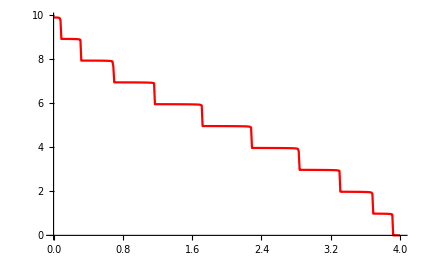

```mathematica
ListLinePlot[Table[{ω,TRA[ω,0]},{ω,Range[0,4,0.01]}],PlotStyle->Red]
```

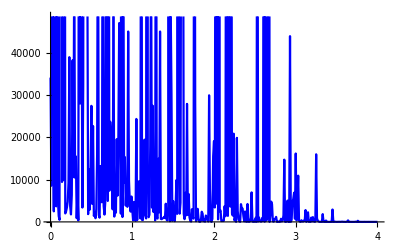

```mathematica
ListLinePlot[Table[{ω,TRA2[ω,0.3]},{ω,Range[0,4,0.01]}],PlotStyle->Blue]
```

```mathematica
Show[%276,%279]
```

```mathematica
TRA2[1,0.3]
```

2858.9

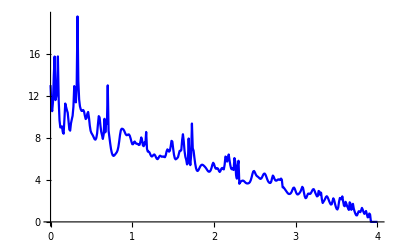

```mathematica
ListLinePlot[Table[{ω,TRA[ω,0.3]},{ω,Range[0,4,0.01]}],PlotStyle->Blue]
```

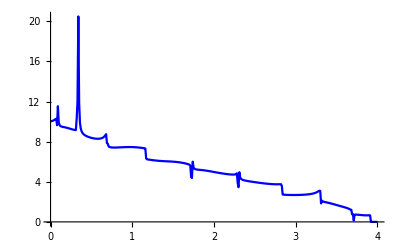

```mathematica
ListLinePlot[Table[{ω,TRA[ω,0.5]},{ω,Range[0,4,0.01]}],PlotStyle->Blue]
```

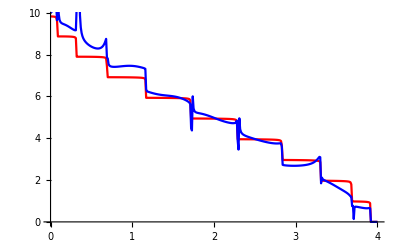

```mathematica
Show[%157,%163]
```

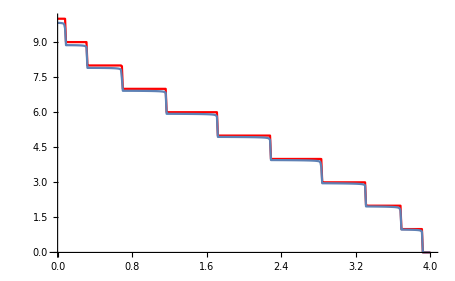

```mathematica
Show[ListLinePlot[Table[{ω,Abs[tr[ω,0.0001,1,0,10]]},{ω,Range[0,4,0.01]}],PlotStyle->Red],%90]
```

```mathematica
greenfunctions[ω_,δ_,t_,ϵ_,m_,ϵ1_,START_,STOP_]:=Module[{Tin=T[1,m],J=SL[ω,δ,t,ϵ,m],b,il,gnk(*,μ1=RandomInteger[{1,m}], μ2=RandomInteger[{1,m}], μ3=RandomInteger[{1,m}], μ4=RandomInteger[{1,m}],μ5=RandomInteger[{1,m}], μ6=RandomInteger[{1,m}], μ7=RandomInteger[{1,m}],μ8=RandomInteger[{1,m}],μ9=RandomInteger[{1,m}], μ10=RandomInteger[{1,m}], μ11=RandomInteger[{1,m}],μ12=RandomInteger[{1,m}], μ13=RandomInteger[{1,m}],μ14=RandomInteger[{1,m}]*)},
imp1:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];
imp2:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];
imp3:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];
imp4:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];
imp5:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];
imp6:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];
imp7:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];
imp8:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];
imp9:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*δ-ϵ1]]];
imp10:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*δ-ϵ1]]];
imp11:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*δ-ϵ1]]];
imp12:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*δ-ϵ1]]];
imp13:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*δ-ϵ1]]];
imp14:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*δ-ϵ1]]];
imp:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{1,1}}->ω+ⅈ*δ-0]]];
list={{imp,imp,imp,imp1,imp3,imp5,imp14,imp,imp,imp,imp2,imp,imp5,imp,imp4,imp,imp12,imp1,imp,imp,imp8,imp,imp,imp8,imp3,imp,imp,imp,imp,imp,imp4,imp,imp11,imp3,imp,imp,imp,imp,imp,imp13,imp7,imp,imp4,imp7,imp9,imp,imp2,imp14,imp5,imp,imp,imp,imp,imp13,imp6,imp,imp,imp10,imp11,imp,imp12,imp,imp,imp14,imp,imp,imp,imp11,imp,imp,imp,imp6,imp,imp1,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp6,imp,imp13,imp9,imp10,imp2,imp10,imp7,imp,imp12,imp,imp8,imp,imp,imp,imp,imp}};
b[n_]:=
Module[{(*J=SL[ω,δ,t,ϵ,m]*)},Do[J=Inverse[IdentityMatrix[m]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,1,n}];
 J=J];
ξ=With[{},Table[b[n],{n,STOP+1}]];
ir:=Inverse[IdentityMatrix[10]-J.T[1,10].ξ[[101]].T[1,10]].J;
gnk[κ_,ι_,Τ_,Μ_]:=Module[{},
gik=Module[{φ=ξ[[κ]].T[1,10].ξ[[κ+1]]},Do[φ=φ.T[1,10].ξ[[l]],{l,κ+2,ι}];
φ=φ];
gik];
gnk[START,STOP,t,m]]
```

```mathematica
greenfunctions[0,0.0001,1,0,10,0,1,100]
```

{{0.000131234+0. ⅈ,0.+0.00251768 ⅈ,0.000418886+0. ⅈ,0.+0.00737844 ⅈ,0.000805518+0. ⅈ,0.+0.0238256 ⅈ,0.00150423+0. ⅈ,0.+0.169532 ⅈ,-0.495863+0. ⅈ,0.-0.843914 ⅈ},{0.+0.00251768 ⅈ,0.00055012+0. ⅈ,0.+0.00989612 ⅈ,0.0012244+0. ⅈ,0.+0.0312041 ⅈ,0.00230975+0. ⅈ,0.+0.193358 ⅈ,-0.494359+0. ⅈ,0.-0.674382 ⅈ,-0.495863+0. ⅈ},{0.000418886+0. ⅈ,0.+0.00989612 ⅈ,0.00135564+0. ⅈ,0.+0.0337218 ⅈ,0.00272863+0. ⅈ,0.+0.200736 ⅈ,-0.493554+0. ⅈ,0.-0.650557 ⅈ,-0.494359+0. ⅈ,0.+0.169532 ⅈ},{0.+0.00737844 ⅈ,0.0012244+0. ⅈ,0.+0.0337218 ⅈ,0.00285987+0. ⅈ,0.+0.203254 ⅈ,-0.493135+0. ⅈ,0.-0.643178 ⅈ,-0.493554+0. ⅈ,0.+0.193358 ⅈ,0.00150423+0. ⅈ},{0.000805518+0. ⅈ,0.+0.0312041 ⅈ,0.00272863+0. ⅈ,0.+0.203254 ⅈ,-0.493004+0. ⅈ,0.-0.640661 ⅈ,-0.493135+0. ⅈ,0.+0.200736 ⅈ,0.00230975+0. ⅈ,0.+0.0238256 ⅈ},{0.+0.0238256 ⅈ,0.00230975+0. ⅈ,0.+0.200736 ⅈ,-0.493135+0. ⅈ,0.-0.640661 ⅈ,-0.493004+0. ⅈ,0.+0.203254 ⅈ,0.00272863+0. ⅈ,0.+0.0312041 ⅈ,0.000805518+0. ⅈ},{0.00150423+0. ⅈ,0.+0.193358 ⅈ,-0.493554+0. ⅈ,0.-0.643178 ⅈ,-0.493135+0. ⅈ,0.+0.203254 ⅈ,0.00285987+0. ⅈ,0.+0.0337218 ⅈ,0.0012244+0. ⅈ,0.+0.00737844 ⅈ},{0.+0.169532 ⅈ,-0.494359+0. ⅈ,0.-0.650557 ⅈ,-0.493554+0. ⅈ,0.+0.200736 ⅈ,0.00272863+0. ⅈ,0.+0.0337218 ⅈ,0.00135564+0. ⅈ,0.+0.00989612 ⅈ,0.000418886+0. ⅈ},{-0.495863+0. ⅈ,0.-0.674382 ⅈ,-0.494359+0. ⅈ,0.+0.193358 ⅈ,0.00230975+0. ⅈ,0.+0.0312041 ⅈ,0.0012244+0. ⅈ,0.+0.00989612 ⅈ,0.00055012+0. ⅈ,0.+0.00251768 ⅈ},{0.-0.843914 ⅈ,-0.495863+0. ⅈ,0.+0.169532 ⅈ,0.00150423+0. ⅈ,0.+0.0238256 ⅈ,0.000805518+0. ⅈ,0.+0.00737844 ⅈ,0.000418886+0. ⅈ,0.+0.00251768 ⅈ,0.000131234+0. ⅈ}}

```mathematica
gik111[κ_,ι_]:=Module[{φ=b1[κ].V.b1[κ+1]},Do[φ=φ.V.b1[l],{l,κ+2,ι}];
φ=φ]
```

```mathematica
gik111[1,100]
```

b1[1].V.b1[2].V.b1[3].V.b1[4].V.b1[5].V.b1[6].V.b1[7].V.b1[8].V.b1[9].V.b1[10].V.b1[11].V.b1[12].V.b1[13].V.b1[14].V.b1[15].V.b1[16].V.b1[17].V.b1[18].V.b1[19].V.b1[20].V.b1[21].V.b1[22].V.b1[23].V.b1[24].V.b1[25].V.b1[26].V.b1[27].V.b1[28].V.b1[29].V.b1[30].V.b1[31].V.b1[32].V.b1[33].V.b1[34].V.b1[35].V.b1[36].V.b1[37].V.b1[38].V.b1[39].V.b1[40].V.b1[41].V.b1[42].V.b1[43].V.b1[44].V.b1[45].V.b1[46].V.b1[47].V.b1[48].V.b1[49].V.b1[50].V.b1[51].V.b1[52].V.b1[53].V.b1[54].V.b1[55].V.b1[56].V.b1[57].V.b1[58].V.b1[59].V.b1[60].V.b1[61].V.b1[62].V.b1[63].V.b1[64].V.b1[65].V.b1[66].V.b1[67].V.b1[68].V.b1[69].V.b1[70].V.b1[71].V.b1[72].V.b1[73].V.b1[74].V.b1[75].V.b1[76].V.b1[77].V.b1[78].V.b1[79].V.b1[80].V.b1[81].V.b1[82].V.b1[83].V.b1[84].V.b1[85].V.b1[86].V.b1[87].V.b1[88].V.b1[89].V.b1[90].V.b1[91].V.b1[92].V.b1[93].V.b1[94].V.b1[95].V.b1[96].V.b1[97].V.b1[98].V.b1[99].V.b1[100]

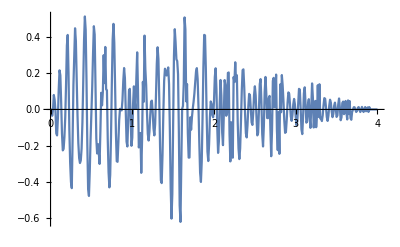

```mathematica
ListLinePlot[Table[{ω,-Im[greenfunctions[ω,0.0001,1,0,10,0,1,100][[1,1]]]},{ω,Range[0,4,0.01]}]]
```

```mathematica
TRA2[ω_,ϵ1_]:=Abs[Tr[Γ[ω].greenfunctions[ω,0.0001,1,0,10,ϵ1,1,100].Γ[ω].ConjugateTranspose[greenfunctions[ω,0.0001,1,0,10,ϵ1,1,100]]]]
```

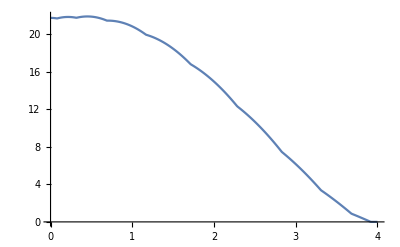

```mathematica
ListLinePlot[Table[{ω,TRA2[ω,0]},{ω,Range[0,4,0.01]}]]
```

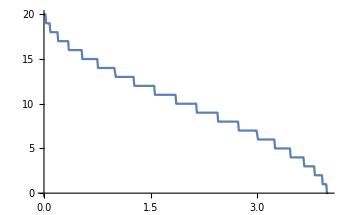

```mathematica
ListLinePlot[Table[{ω,Abs[tr[ω,0.0001,1,0,20]]},{ω,Range[0,4,0.01]}]]
```

```mathematica
LEFT[1.6,0.0001,1,0,20]
```

{{0.483268-0.487021 ⅈ,-0.109865-0.395884 ⅈ,-0.216368+0.000104526 ⅈ,0.0025665+0.124646 ⅈ,0.0728843-0.0143304 ⅈ,-0.0208033-0.0568908 ⅈ,-0.0338025+0.0255238 ⅈ,0.0227662+0.0297846 ⅈ,0.0142494-0.0274045 ⅈ,-0.0196025-0.0134178 ⅈ,-0.00317989+0.025796 ⅈ,0.0145215+0.00224635 ⅈ,-0.00274882-0.0222819 ⅈ,-0.00905197+0.00570799 ⅈ,0.00507448+0.0175832 ⅈ,0.00416245-0.0112749 ⅈ,-0.00481226-0.0121144 ⅈ,-0.000529404+0.0148401 ⅈ,0.00283621+0.00617119 ⅈ,-0.00139983-0.0165858 ⅈ},{-0.109865-0.395884 ⅈ,0.266901-0.486916 ⅈ,-0.107298-0.271239 ⅈ,-0.143483-0.0142259 ⅈ,-0.0182368+0.0677547 ⅈ,0.0390818+0.0111934 ⅈ,0.00196293-0.0271062 ⅈ,-0.0195531-0.00188066 ⅈ,0.00316367+0.0163668 ⅈ,0.0110695-0.00160844 ⅈ,-0.00508103-0.0111714 ⅈ,-0.00592871+0.0035141 ⅈ,0.00546951+0.00795434 ⅈ,0.00232566-0.00469874 ⅈ,-0.00488951-0.00556693 ⅈ,0.00026222+0.00546882 ⅈ,0.00363305+0.00356519 ⅈ,-0.00197605-0.00594318 ⅈ,-0.00192923-0.00174572 ⅈ,0.00283621+0.00617119 ⅈ},{-0.216368+0.000104526 ⅈ,-0.107298-0.271239 ⅈ,0.339785-0.501246 ⅈ,-0.128101-0.32813 ⅈ,-0.177286+0.0112979 ⅈ,0.00452942+0.0975393 ⅈ,0.0533312-0.0162111 ⅈ,-0.0176396-0.040524 ⅈ,-0.022733+0.0239154 ⅈ,0.0176851+0.0186132 ⅈ,0.00832069-0.0238904 ⅈ,-0.014133-0.00546346 ⅈ,-0.000854227+0.0210973 ⅈ,0.00963196-0.00332058 ⅈ,-0.0024866-0.0168131 ⅈ,-0.00541892+0.00927318 ⅈ,0.00309843+0.01164 ⅈ,0.00223322-0.0130206 ⅈ,-0.00197605-0.00594318 ⅈ,-0.000529404+0.0148401 ⅈ},{0.0025665+0.124646 ⅈ,-0.143483-0.0142259 ⅈ,-0.128101-0.32813 ⅈ,0.305982-0.475723 ⅈ,-0.105335-0.298345 ⅈ,-0.163036-0.0161065 ⅈ,-0.0150731+0.0841215 ⅈ,0.0501513+0.00958496 ⅈ,-0.0031181-0.0382777 ⅈ,-0.0254818+0.00163344 ⅈ,0.00863318+0.0243211 ⅈ,0.0133952-0.00630718 ⅈ,-0.00997055-0.0167384 ⅈ,-0.00566649+0.00898292 ⅈ,0.00910256+0.0115195 ⅈ,0.000349615-0.0106419 ⅈ,-0.00681875-0.00731265 ⅈ,0.00309843+0.01164 ⅈ,0.00363305+0.00356519 ⅈ,-0.00481226-0.0121144 ⅈ},{0.0728843-0.0143304 ⅈ,-0.0182368+0.0677547 ⅈ,-0.177286+0.0112979 ⅈ,-0.105335-0.298345 ⅈ,0.320232-0.503127 ⅈ,-0.124938-0.311763 ⅈ,-0.166216+0.00968949 ⅈ,-0.000551608+0.0863679 ⅈ,0.0474024-0.012697 ⅈ,-0.0121701-0.0325697 ⅈ,-0.0204074+0.0192166 ⅈ,0.0127956+0.0130462 ⅈ,0.0085829-0.0184216 ⅈ,-0.0104999-0.00189826 ⅈ,-0.00283028+0.0151541 ⅈ,0.00770273-0.0050663 ⅈ,0.000349615-0.0106419 ⅈ,-0.00541892+0.00927318 ⅈ,0.00026222+0.00546882 ⅈ,0.00416245-0.0112749 ⅈ},{-0.0208033-0.0568908 ⅈ,0.0390818+0.0111934 ⅈ,0.00452942+0.0975393 ⅈ,-0.163036-0.0161065 ⅈ,-0.124938-0.311763 ⅈ,0.317052-0.477331 ⅈ,-0.110416-0.309517 ⅈ,-0.168965-0.0125924 ⅈ,-0.00960357+0.0920758 ⅈ,0.0524769+0.00488622 ⅈ,-0.00800762-0.0438446 ⅈ,-0.0252196+0.00710226 ⅈ,0.0122662+0.0278863 ⅈ,0.0114191-0.0122504 ⅈ,-0.0118998-0.0184841 ⅈ,-0.00283028+0.0151541 ⅈ,0.00910256+0.0115195 ⅈ,-0.0024866-0.0168131 ⅈ,-0.00488951-0.00556693 ⅈ,0.00507448+0.0175832 ⅈ},{-0.0338025+0.0255238 ⅈ,0.00196293-0.0271062 ⅈ,0.0533312-0.0162111 ⅈ,-0.0150731+0.0841215 ⅈ,-0.166216+0.00968949 ⅈ,-0.110416-0.309517 ⅈ,0.314303-0.499613 ⅈ,-0.119468-0.303809 ⅈ,-0.163891+0.00499075 ⅈ,-0.00544112+0.0808009 ⅈ,0.0476647-0.00722815 ⅈ,-0.00853702-0.0290045 ⅈ,-0.0223834+0.0132734 ⅈ,0.0108664+0.0113005 ⅈ,0.0114191-0.0122504 ⅈ,-0.0104999-0.00189826 ⅈ,-0.00566649+0.00898292 ⅈ,0.00963196-0.00332058 ⅈ,0.00232566-0.00469874 ⅈ,-0.00905197+0.00570799 ⅈ},{0.0227662+0.0297846 ⅈ,-0.0195531-0.00188066 ⅈ,-0.0176396-0.040524 ⅈ,0.0501513+0.00958496 ⅈ,-0.000551608+0.0863679 ⅈ,-0.168965-0.0125924 ⅈ,-0.119468-0.303809 ⅈ,0.319378-0.48203 ⅈ,-0.115306-0.315083 ⅈ,-0.168703-0.00712362 ⅈ,-0.00597053+0.095641 ⅈ,0.0505009-0.00105696 ⅈ,-0.00993685-0.0455903 ⅈ,-0.0223834+0.0132734 ⅈ,0.0122662+0.0278863 ⅈ,0.0085829-0.0184216 ⅈ,-0.00997055-0.0167384 ⅈ,-0.000854227+0.0210973 ⅈ,0.00546951+0.00795434 ⅈ,-0.00274882-0.0222819 ⅈ},{0.0142494-0.0274045 ⅈ,0.00316367+0.0163668 ⅈ,-0.022733+0.0239154 ⅈ,-0.0031181-0.0382777 ⅈ,0.0474024-0.012697 ⅈ,-0.00960357+0.0920758 ⅈ,-0.163891+0.00499075 ⅈ,-0.115306-0.315083 ⅈ,0.314565-0.494144 ⅈ,-0.115835-0.300243 ⅈ,-0.165867-0.000952434 ⅈ,-0.00737036+0.0790552 ⅈ,0.0505009-0.00105696 ⅈ,-0.00853702-0.0290045 ⅈ,-0.0252196+0.00710226 ⅈ,0.0127956+0.0130462 ⅈ,0.0133952-0.00630718 ⅈ,-0.014133-0.00546346 ⅈ,-0.00592871+0.0035141 ⅈ,0.0145215+0.00224635 ⅈ},{-0.0196025-0.0134178 ⅈ,0.0110695-0.00160844 ⅈ,0.0176851+0.0186132 ⅈ,-0.0254818+0.00163344 ⅈ,-0.0121701-0.0325697 ⅈ,0.0524769+0.00488622 ⅈ,-0.00544112+0.0808009 ⅈ,-0.168703-0.00712362 ⅈ,-0.115835-0.300243 ⅈ,0.317402-0.487973 ⅈ,-0.117235-0.316829 ⅈ,-0.165867-0.000952434 ⅈ,-0.00597053+0.095641 ⅈ,0.0476647-0.00722815 ⅈ,-0.00800762-0.0438446 ⅈ,-0.0204074+0.0192166 ⅈ,0.00863318+0.0243211 ⅈ,0.00832069-0.0238904 ⅈ,-0.00508103-0.0111714 ⅈ,-0.00317989+0.025796 ⅈ},{-0.00317989+0.025796 ⅈ,-0.00508103-0.0111714 ⅈ,0.00832069-0.0238904 ⅈ,0.00863318+0.0243211 ⅈ,-0.0204074+0.0192166 ⅈ,-0.00800762-0.0438446 ⅈ,0.0476647-0.00722815 ⅈ,-0.00597053+0.095641 ⅈ,-0.165867-0.000952434 ⅈ,-0.117235-0.316829 ⅈ,0.317402-0.487973 ⅈ,-0.115835-0.300243 ⅈ,-0.168703-0.00712362 ⅈ,-0.00544112+0.0808009 ⅈ,0.0524769+0.00488622 ⅈ,-0.0121701-0.0325697 ⅈ,-0.0254818+0.00163344 ⅈ,0.0176851+0.0186132 ⅈ,0.0110695-0.00160844 ⅈ,-0.0196025-0.0134178 ⅈ},{0.0145215+0.00224635 ⅈ,-0.00592871+0.0035141 ⅈ,-0.014133-0.00546346 ⅈ,0.0133952-0.00630718 ⅈ,0.0127956+0.0130462 ⅈ,-0.0252196+0.00710226 ⅈ,-0.00853702-0.0290045 ⅈ,0.0505009-0.00105696 ⅈ,-0.00737036+0.0790552 ⅈ,-0.165867-0.000952434 ⅈ,-0.115835-0.300243 ⅈ,0.314565-0.494144 ⅈ,-0.115306-0.315083 ⅈ,-0.163891+0.00499075 ⅈ,-0.00960357+0.0920758 ⅈ,0.0474024-0.012697 ⅈ,-0.0031181-0.0382777 ⅈ,-0.022733+0.0239154 ⅈ,0.00316367+0.0163668 ⅈ,0.0142494-0.0274045 ⅈ},{-0.00274882-0.0222819 ⅈ,0.00546951+0.00795434 ⅈ,-0.000854227+0.0210973 ⅈ,-0.00997055-0.0167384 ⅈ,0.0085829-0.0184216 ⅈ,0.0122662+0.0278863 ⅈ,-0.0223834+0.0132734 ⅈ,-0.00993685-0.0455903 ⅈ,0.0505009-0.00105696 ⅈ,-0.00597053+0.095641 ⅈ,-0.168703-0.00712362 ⅈ,-0.115306-0.315083 ⅈ,0.319378-0.48203 ⅈ,-0.119468-0.303809 ⅈ,-0.168965-0.0125924 ⅈ,-0.000551608+0.0863679 ⅈ,0.0501513+0.00958496 ⅈ,-0.0176396-0.040524 ⅈ,-0.0195531-0.00188066 ⅈ,0.0227662+0.0297846 ⅈ},{-0.00905197+0.00570799 ⅈ,0.00232566-0.00469874 ⅈ,0.00963196-0.00332058 ⅈ,-0.00566649+0.00898292 ⅈ,-0.0104999-0.00189826 ⅈ,0.0114191-0.0122504 ⅈ,0.0108664+0.0113005 ⅈ,-0.0223834+0.0132734 ⅈ,-0.00853702-0.0290045 ⅈ,0.0476647-0.00722815 ⅈ,-0.00544112+0.0808009 ⅈ,-0.163891+0.00499075 ⅈ,-0.119468-0.303809 ⅈ,0.314303-0.499613 ⅈ,-0.110416-0.309517 ⅈ,-0.166216+0.00968949 ⅈ,-0.0150731+0.0841215 ⅈ,0.0533312-0.0162111 ⅈ,0.00196293-0.0271062 ⅈ,-0.0338025+0.0255238 ⅈ},{0.00507448+0.0175832 ⅈ,-0.00488951-0.00556693 ⅈ,-0.0024866-0.0168131 ⅈ,0.00910256+0.0115195 ⅈ,-0.00283028+0.0151541 ⅈ,-0.0118998-0.0184841 ⅈ,0.0114191-0.0122504 ⅈ,0.0122662+0.0278863 ⅈ,-0.0252196+0.00710226 ⅈ,-0.00800762-0.0438446 ⅈ,0.0524769+0.00488622 ⅈ,-0.00960357+0.0920758 ⅈ,-0.168965-0.0125924 ⅈ,-0.110416-0.309517 ⅈ,0.317052-0.477331 ⅈ,-0.124938-0.311763 ⅈ,-0.163036-0.0161065 ⅈ,0.00452942+0.0975393 ⅈ,0.0390818+0.0111934 ⅈ,-0.0208033-0.0568908 ⅈ},{0.00416245-0.0112749 ⅈ,0.00026222+0.00546882 ⅈ,-0.00541892+0.00927318 ⅈ,0.000349615-0.0106419 ⅈ,0.00770273-0.0050663 ⅈ,-0.00283028+0.0151541 ⅈ,-0.0104999-0.00189826 ⅈ,0.0085829-0.0184216 ⅈ,0.0127956+0.0130462 ⅈ,-0.0204074+0.0192166 ⅈ,-0.0121701-0.0325697 ⅈ,0.0474024-0.012697 ⅈ,-0.000551608+0.0863679 ⅈ,-0.166216+0.00968949 ⅈ,-0.124938-0.311763 ⅈ,0.320232-0.503127 ⅈ,-0.105335-0.298345 ⅈ,-0.177286+0.0112979 ⅈ,-0.0182368+0.0677547 ⅈ,0.0728843-0.0143304 ⅈ},{-0.00481226-0.0121144 ⅈ,0.00363305+0.00356519 ⅈ,0.00309843+0.01164 ⅈ,-0.00681875-0.00731265 ⅈ,0.000349615-0.0106419 ⅈ,0.00910256+0.0115195 ⅈ,-0.00566649+0.00898292 ⅈ,-0.00997055-0.0167384 ⅈ,0.0133952-0.00630718 ⅈ,0.00863318+0.0243211 ⅈ,-0.0254818+0.00163344 ⅈ,-0.0031181-0.0382777 ⅈ,0.0501513+0.00958496 ⅈ,-0.0150731+0.0841215 ⅈ,-0.163036-0.0161065 ⅈ,-0.105335-0.298345 ⅈ,0.305982-0.475723 ⅈ,-0.128101-0.32813 ⅈ,-0.143483-0.0142259 ⅈ,0.0025665+0.124646 ⅈ},{-0.000529404+0.0148401 ⅈ,-0.00197605-0.00594318 ⅈ,0.00223322-0.0130206 ⅈ,0.00309843+0.01164 ⅈ,-0.00541892+0.00927318 ⅈ,-0.0024866-0.0168131 ⅈ,0.00963196-0.00332058 ⅈ,-0.000854227+0.0210973 ⅈ,-0.014133-0.00546346 ⅈ,0.00832069-0.0238904 ⅈ,0.0176851+0.0186132 ⅈ,-0.022733+0.0239154 ⅈ,-0.0176396-0.040524 ⅈ,0.0533312-0.0162111 ⅈ,0.00452942+0.0975393 ⅈ,-0.177286+0.0112979 ⅈ,-0.128101-0.32813 ⅈ,0.339785-0.501246 ⅈ,-0.107298-0.271239 ⅈ,-0.216368+0.000104526 ⅈ},{0.00283621+0.00617119 ⅈ,-0.00192923-0.00174572 ⅈ,-0.00197605-0.00594318 ⅈ,0.00363305+0.00356519 ⅈ,0.00026222+0.00546882 ⅈ,-0.00488951-0.00556693 ⅈ,0.00232566-0.00469874 ⅈ,0.00546951+0.00795434 ⅈ,-0.00592871+0.0035141 ⅈ,-0.00508103-0.0111714 ⅈ,0.0110695-0.00160844 ⅈ,0.00316367+0.0163668 ⅈ,-0.0195531-0.00188066 ⅈ,0.00196293-0.0271062 ⅈ,0.0390818+0.0111934 ⅈ,-0.0182368+0.0677547 ⅈ,-0.143483-0.0142259 ⅈ,-0.107298-0.271239 ⅈ,0.266901-0.486916 ⅈ,-0.109865-0.395884 ⅈ},{-0.00139983-0.0165858 ⅈ,0.00283621+0.00617119 ⅈ,-0.000529404+0.0148401 ⅈ,-0.00481226-0.0121144 ⅈ,0.00416245-0.0112749 ⅈ,0.00507448+0.0175832 ⅈ,-0.00905197+0.00570799 ⅈ,-0.00274882-0.0222819 ⅈ,0.0145215+0.00224635 ⅈ,-0.00317989+0.025796 ⅈ,-0.0196025-0.0134178 ⅈ,0.0142494-0.0274045 ⅈ,0.0227662+0.0297846 ⅈ,-0.0338025+0.0255238 ⅈ,-0.0208033-0.0568908 ⅈ,0.0728843-0.0143304 ⅈ,0.0025665+0.124646 ⅈ,-0.216368+0.000104526 ⅈ,-0.109865-0.395884 ⅈ,0.483268-0.487021 ⅈ}}

```mathematica
SL[1,0.0001,1,0,20]
```

{{0.382877-0.662623 ⅈ,-0.319165-0.3419 ⅈ,-0.168162+0.144309 ⅈ,0.0976838+0.0572382 ⅈ,-0.0149232-0.0709611 ⅈ,-0.0368604+0.0288084 ⅈ,0.0411655+0.021371 ⅈ,-0.012892-0.0361553 ⅈ,-0.0173503+0.014507 ⅈ,0.0262734+0.0153099 ⅈ,-0.0118928-0.0244316 ⅈ,-0.00967053+0.00838237 ⅈ,0.0196879+0.0133656 ⅈ,-0.0116494-0.0189072 ⅈ,-0.00541293+0.00478161 ⅈ,0.0161212+0.0128545 ⅈ,-0.0119284-0.0158668 ⅈ,-0.00246424+0.0021974 ⅈ,0.01399+0.013141 ⅈ,-0.0126796-0.0140993 ⅈ},{-0.319165-0.3419 ⅈ,0.214714-0.518314 ⅈ,-0.221481-0.284662 ⅈ,-0.183086+0.0733477 ⅈ,0.0608234+0.0860466 ⅈ,0.0262423-0.0495901 ⅈ,-0.0497524-0.0073469 ⅈ,0.0238152+0.035878 ⅈ,0.0133814-0.0208454 ⅈ,-0.0292431-0.00992463 ⅈ,0.0166029+0.0236922 ⅈ,0.00779509-0.0110661 ⅈ,-0.0213199-0.0105248 ⅈ,0.0142749+0.0181472 ⅈ,0.00447177-0.00605268 ⅈ,-0.0173413-0.0110852 ⅈ,0.0136569+0.0150519 ⅈ,0.00206162-0.00272576 ⅈ,-0.0151438-0.0119019 ⅈ,0.01399+0.013141 ⅈ},{-0.168162+0.144309 ⅈ,-0.221481-0.284662 ⅈ,0.199791-0.589275 ⅈ,-0.258342-0.255854 ⅈ,-0.14192+0.0947187 ⅈ,0.0479314+0.0498913 ⅈ,0.00889197-0.0350832 ⅈ,-0.023479+0.00796297 ⅈ,0.0119224+0.0114463 ⅈ,0.00371086-0.012463 ⅈ,-0.0095552+0.00344093 ⅈ,0.00495347+0.00478504 ⅈ,0.00238217-0.00628445 ⅈ,-0.00519876+0.00232969 ⅈ,0.00234656+0.00228037 ⅈ,0.00200753-0.00385528 ⅈ,-0.00335131+0.00205584 ⅈ,0.000977356+0.000952665 ⅈ,0.00206162-0.00272576 ⅈ,-0.00246424+0.0021974 ⅈ},{0.0976838+0.0572382 ⅈ,-0.183086+0.0733477 ⅈ,-0.258342-0.255854 ⅈ,0.240957-0.567904 ⅈ,-0.271234-0.292009 ⅈ,-0.15927+0.109226 ⅈ,0.0742048+0.0652012 ⅈ,-0.00300079-0.0595148 ⅈ,-0.0331496+0.0163453 ⅈ,0.0316103+0.0248119 ⅈ,-0.00793853-0.0313702 ⅈ,-0.0149681+0.00822253 ⅈ,0.0210746+0.0176396 ⅈ,-0.0095462-0.0221512 ⅈ,-0.007663+0.0045271 ⅈ,0.0163366+0.0154214 ⅈ,-0.010672-0.0179545 ⅈ,-0.00335131+0.00205584 ⅈ,0.0136569+0.0150519 ⅈ,-0.0119284-0.0158668 ⅈ},{-0.0149232-0.0709611 ⅈ,0.0608234+0.0860466 ⅈ,-0.14192+0.0947187 ⅈ,-0.271234-0.292009 ⅈ,0.223606-0.553397 ⅈ,-0.24496-0.276699 ⅈ,-0.171163+0.0847941 ⅈ,0.0645343+0.0735836 ⅈ,0.0166871-0.0461492 ⅈ,-0.0447989-0.00256186 ⅈ,0.0261974+0.0295935 ⅈ,0.00818263-0.0185157 ⅈ,-0.0268965-0.00764426 ⅈ,0.0186104+0.019837 ⅈ,0.00444379-0.00901022 ⅈ,-0.0203426-0.00957217 ⅈ,0.0163366+0.0154214 ⅈ,0.00200753-0.00385528 ⅈ,-0.0173413-0.0110852 ⅈ,0.0161212+0.0128545 ⅈ},{-0.0368604+0.0288084 ⅈ,0.0262423-0.0495901 ⅈ,0.0479314+0.0498913 ⅈ,-0.15927+0.109226 ⅈ,-0.24496-0.276699 ⅈ,0.211714-0.577829 ⅈ,-0.254631-0.268317 ⅈ,-0.151475+0.0981596 ⅈ,0.0528849+0.0546764 ⅈ,0.0112741-0.0413676 ⅈ,-0.0286778+0.0102927 ⅈ,0.014269+0.0137267 ⅈ,0.00571839-0.0163183 ⅈ,-0.0129065+0.00549677 ⅈ,0.00593082+0.0057377 ⅈ,0.00444379-0.00901022 ⅈ,-0.007663+0.0045271 ⅈ,0.00234656+0.00228037 ⅈ,0.00447177-0.00605268 ⅈ,-0.00541293+0.00478161 ⅈ},{0.0411655+0.021371 ⅈ,-0.0497524-0.0073469 ⅈ,0.00889197-0.0350832 ⅈ,0.0742048+0.0652012 ⅈ,-0.171163+0.0847941 ⅈ,-0.254631-0.268317 ⅈ,0.231401-0.564463 ⅈ,-0.26628-0.287224 ⅈ,-0.156888+0.102941 ⅈ,0.069006+0.0675309 ⅈ,-0.000654229-0.0572344 ⅈ,-0.031142+0.0124901 ⅈ,0.028259+0.0268677 ⅈ,-0.00696118-0.0304176 ⅈ,-0.0129065+0.00549677 ⅈ,0.0186104+0.019837 ⅈ,-0.0095462-0.0221512 ⅈ,-0.00519876+0.00232969 ⅈ,0.0142749+0.0181472 ⅈ,-0.0116494-0.0189072 ⅈ},{-0.012892-0.0361553 ⅈ,0.0238152+0.035878 ⅈ,-0.023479+0.00796297 ⅈ,-0.00300079-0.0595148 ⅈ,0.0645343+0.0735836 ⅈ,-0.151475+0.0981596 ⅈ,-0.26628-0.287224 ⅈ,0.225989-0.559681 ⅈ,-0.250159-0.274369 ⅈ,-0.168817+0.0870744 ⅈ,0.0665418+0.0697283 ⅈ,0.0133358-0.0440934 ⅈ,-0.0438216-0.0016092 ⅈ,0.028259+0.0268677 ⅈ,0.00571839-0.0163183 ⅈ,-0.0268965-0.00764426 ⅈ,0.0210746+0.0176396 ⅈ,0.00238217-0.00628445 ⅈ,-0.0213199-0.0105248 ⅈ,0.0196879+0.0133656 ⅈ},{-0.0173503+0.014507 ⅈ,0.0133814-0.0208454 ⅈ,0.0119224+0.0114463 ⅈ,-0.0331496+0.0163453 ⅈ,0.0166871-0.0461492 ⅈ,0.0528849+0.0546764 ⅈ,-0.156888+0.102941 ⅈ,-0.250159-0.274369 ⅈ,0.21406-0.575548 ⅈ,-0.252623-0.272172 ⅈ,-0.154827+0.100215 ⅈ,0.0538622+0.055629 ⅈ,0.0133358-0.0440934 ⅈ,-0.031142+0.0124901 ⅈ,0.014269+0.0137267 ⅈ,0.00818263-0.0185157 ⅈ,-0.0149681+0.00822253 ⅈ,0.00495347+0.00478504 ⅈ,0.00779509-0.0110661 ⅈ,-0.00967053+0.00838237 ⅈ},{0.0262734+0.0153099 ⅈ,-0.0292431-0.00992463 ⅈ,0.00371086-0.012463 ⅈ,0.0316103+0.0248119 ⅈ,-0.0447989-0.00256186 ⅈ,0.0112741-0.0413676 ⅈ,0.069006+0.0675309 ⅈ,-0.168817+0.0870744 ⅈ,-0.252623-0.272172 ⅈ,0.22805-0.562407 ⅈ,-0.265303-0.286271 ⅈ,-0.154827+0.100215 ⅈ,0.0665418+0.0697283 ⅈ,-0.000654229-0.0572344 ⅈ,-0.0286778+0.0102927 ⅈ,0.0261974+0.0295935 ⅈ,-0.00793853-0.0313702 ⅈ,-0.0095552+0.00344093 ⅈ,0.0166029+0.0236922 ⅈ,-0.0118928-0.0244316 ⅈ},{-0.0118928-0.0244316 ⅈ,0.0166029+0.0236922 ⅈ,-0.0095552+0.00344093 ⅈ,-0.00793853-0.0313702 ⅈ,0.0261974+0.0295935 ⅈ,-0.0286778+0.0102927 ⅈ,-0.000654229-0.0572344 ⅈ,0.0665418+0.0697283 ⅈ,-0.154827+0.100215 ⅈ,-0.265303-0.286271 ⅈ,0.22805-0.562407 ⅈ,-0.252623-0.272172 ⅈ,-0.168817+0.0870744 ⅈ,0.069006+0.0675309 ⅈ,0.0112741-0.0413676 ⅈ,-0.0447989-0.00256186 ⅈ,0.0316103+0.0248119 ⅈ,0.00371086-0.012463 ⅈ,-0.0292431-0.00992463 ⅈ,0.0262734+0.0153099 ⅈ},{-0.00967053+0.00838237 ⅈ,0.00779509-0.0110661 ⅈ,0.00495347+0.00478504 ⅈ,-0.0149681+0.00822253 ⅈ,0.00818263-0.0185157 ⅈ,0.014269+0.0137267 ⅈ,-0.031142+0.0124901 ⅈ,0.0133358-0.0440934 ⅈ,0.0538622+0.055629 ⅈ,-0.154827+0.100215 ⅈ,-0.252623-0.272172 ⅈ,0.21406-0.575548 ⅈ,-0.250159-0.274369 ⅈ,-0.156888+0.102941 ⅈ,0.0528849+0.0546764 ⅈ,0.0166871-0.0461492 ⅈ,-0.0331496+0.0163453 ⅈ,0.0119224+0.0114463 ⅈ,0.0133814-0.0208454 ⅈ,-0.0173503+0.014507 ⅈ},{0.0196879+0.0133656 ⅈ,-0.0213199-0.0105248 ⅈ,0.00238217-0.00628445 ⅈ,0.0210746+0.0176396 ⅈ,-0.0268965-0.00764426 ⅈ,0.00571839-0.0163183 ⅈ,0.028259+0.0268677 ⅈ,-0.0438216-0.0016092 ⅈ,0.0133358-0.0440934 ⅈ,0.0665418+0.0697283 ⅈ,-0.168817+0.0870744 ⅈ,-0.250159-0.274369 ⅈ,0.225989-0.559681 ⅈ,-0.26628-0.287224 ⅈ,-0.151475+0.0981596 ⅈ,0.0645343+0.0735836 ⅈ,-0.00300079-0.0595148 ⅈ,-0.023479+0.00796297 ⅈ,0.0238152+0.035878 ⅈ,-0.012892-0.0361553 ⅈ},{-0.0116494-0.0189072 ⅈ,0.0142749+0.0181472 ⅈ,-0.00519876+0.00232969 ⅈ,-0.0095462-0.0221512 ⅈ,0.0186104+0.019837 ⅈ,-0.0129065+0.00549677 ⅈ,-0.00696118-0.0304176 ⅈ,0.028259+0.0268677 ⅈ,-0.031142+0.0124901 ⅈ,-0.000654229-0.0572344 ⅈ,0.069006+0.0675309 ⅈ,-0.156888+0.102941 ⅈ,-0.26628-0.287224 ⅈ,0.231401-0.564463 ⅈ,-0.254631-0.268317 ⅈ,-0.171163+0.0847941 ⅈ,0.0742048+0.0652012 ⅈ,0.00889197-0.0350832 ⅈ,-0.0497524-0.0073469 ⅈ,0.0411655+0.021371 ⅈ},{-0.00541293+0.00478161 ⅈ,0.00447177-0.00605268 ⅈ,0.00234656+0.00228037 ⅈ,-0.007663+0.0045271 ⅈ,0.00444379-0.00901022 ⅈ,0.00593082+0.0057377 ⅈ,-0.0129065+0.00549677 ⅈ,0.00571839-0.0163183 ⅈ,0.014269+0.0137267 ⅈ,-0.0286778+0.0102927 ⅈ,0.0112741-0.0413676 ⅈ,0.0528849+0.0546764 ⅈ,-0.151475+0.0981596 ⅈ,-0.254631-0.268317 ⅈ,0.211714-0.577829 ⅈ,-0.24496-0.276699 ⅈ,-0.15927+0.109226 ⅈ,0.0479314+0.0498913 ⅈ,0.0262423-0.0495901 ⅈ,-0.0368604+0.0288084 ⅈ},{0.0161212+0.0128545 ⅈ,-0.0173413-0.0110852 ⅈ,0.00200753-0.00385528 ⅈ,0.0163366+0.0154214 ⅈ,-0.0203426-0.00957217 ⅈ,0.00444379-0.00901022 ⅈ,0.0186104+0.019837 ⅈ,-0.0268965-0.00764426 ⅈ,0.00818263-0.0185157 ⅈ,0.0261974+0.0295935 ⅈ,-0.0447989-0.00256186 ⅈ,0.0166871-0.0461492 ⅈ,0.0645343+0.0735836 ⅈ,-0.171163+0.0847941 ⅈ,-0.24496-0.276699 ⅈ,0.223606-0.553397 ⅈ,-0.271234-0.292009 ⅈ,-0.14192+0.0947187 ⅈ,0.0608234+0.0860466 ⅈ,-0.0149232-0.0709611 ⅈ},{-0.0119284-0.0158668 ⅈ,0.0136569+0.0150519 ⅈ,-0.00335131+0.00205584 ⅈ,-0.010672-0.0179545 ⅈ,0.0163366+0.0154214 ⅈ,-0.007663+0.0045271 ⅈ,-0.0095462-0.0221512 ⅈ,0.0210746+0.0176396 ⅈ,-0.0149681+0.00822253 ⅈ,-0.00793853-0.0313702 ⅈ,0.0316103+0.0248119 ⅈ,-0.0331496+0.0163453 ⅈ,-0.00300079-0.0595148 ⅈ,0.0742048+0.0652012 ⅈ,-0.15927+0.109226 ⅈ,-0.271234-0.292009 ⅈ,0.240957-0.567904 ⅈ,-0.258342-0.255854 ⅈ,-0.183086+0.0733477 ⅈ,0.0976838+0.0572382 ⅈ},{-0.00246424+0.0021974 ⅈ,0.00206162-0.00272576 ⅈ,0.000977356+0.000952665 ⅈ,-0.00335131+0.00205584 ⅈ,0.00200753-0.00385528 ⅈ,0.00234656+0.00228037 ⅈ,-0.00519876+0.00232969 ⅈ,0.00238217-0.00628445 ⅈ,0.00495347+0.00478504 ⅈ,-0.0095552+0.00344093 ⅈ,0.00371086-0.012463 ⅈ,0.0119224+0.0114463 ⅈ,-0.023479+0.00796297 ⅈ,0.00889197-0.0350832 ⅈ,0.0479314+0.0498913 ⅈ,-0.14192+0.0947187 ⅈ,-0.258342-0.255854 ⅈ,0.199791-0.589275 ⅈ,-0.221481-0.284662 ⅈ,-0.168162+0.144309 ⅈ},{0.01399+0.013141 ⅈ,-0.0151438-0.0119019 ⅈ,0.00206162-0.00272576 ⅈ,0.0136569+0.0150519 ⅈ,-0.0173413-0.0110852 ⅈ,0.00447177-0.00605268 ⅈ,0.0142749+0.0181472 ⅈ,-0.0213199-0.0105248 ⅈ,0.00779509-0.0110661 ⅈ,0.0166029+0.0236922 ⅈ,-0.0292431-0.00992463 ⅈ,0.0133814-0.0208454 ⅈ,0.0238152+0.035878 ⅈ,-0.0497524-0.0073469 ⅈ,0.0262423-0.0495901 ⅈ,0.0608234+0.0860466 ⅈ,-0.183086+0.0733477 ⅈ,-0.221481-0.284662 ⅈ,0.214714-0.518314 ⅈ,-0.319165-0.3419 ⅈ},{-0.0126796-0.0140993 ⅈ,0.01399+0.013141 ⅈ,-0.00246424+0.0021974 ⅈ,-0.0119284-0.0158668 ⅈ,0.0161212+0.0128545 ⅈ,-0.00541293+0.00478161 ⅈ,-0.0116494-0.0189072 ⅈ,0.0196879+0.0133656 ⅈ,-0.00967053+0.00838237 ⅈ,-0.0118928-0.0244316 ⅈ,0.0262734+0.0153099 ⅈ,-0.0173503+0.014507 ⅈ,-0.012892-0.0361553 ⅈ,0.0411655+0.021371 ⅈ,-0.0368604+0.0288084 ⅈ,-0.0149232-0.0709611 ⅈ,0.0976838+0.0572382 ⅈ,-0.168162+0.144309 ⅈ,-0.319165-0.3419 ⅈ,0.382877-0.662623 ⅈ}}

```mathematica
device1[ω_,ϵ1_,m_]:=Module[{Tin=T[1,m],T1=T[1,m],μ1=RandomInteger[{1,20}], μ2=RandomInteger[{1,20}], μ3=RandomInteger[{1,20}], μ4=RandomInteger[{1,20}],μ5=RandomInteger[{1,20}], μ6=RandomInteger[{1,20}], μ7=RandomInteger[{1,20}],μ8=RandomInteger[{1,20}], μ9=RandomInteger[{1,20}], μ10=RandomInteger[{1,20}], μ11=RandomInteger[{1,20}],μ12=RandomInteger[{1,20}], μ13=RandomInteger[{1,20}], μ14=RandomInteger[{1,20}],list,b2},
imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]];
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]];
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]];
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]];
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]];
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]];
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]];
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]];
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]];
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]];
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{10,10}}->ω+ⅈ*0.0001-0]]];
b2=Module[{},list={RandomSample[{imp,imp,imp,imp,imp3}]};
sl1= Module[{J=SL[ω,0.0001,1,0,m]},Do[J=Inverse[IdentityMatrix[m]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,1,5}];
 J=J];
Il1:=Inverse[IdentityMatrix[m]-sl1.T1.SL[ω,0.0001,1,0,m].T1].sl1;
Ir1:=Inverse[IdentityMatrix[m]-SL[ω,0.0001,1,0,m].T1.sl1.T1].SL[ω,0.0001,1,0,m];gdd1:=Il1-ConjugateTranspose[Il1];grr1:=Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SL[ω,0.0001,1,0,m].T1.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]>tr[ω,0.0001,1,0,m],tr[ω,0.0001,1,0,m],Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]]];
b2]
```

```mathematica
Table[{ω,Mean[Table[device1[ω,0.5,20],2000]]},{ω,Range[0,4,0.01]}]
```

```mathematica
Export["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/1imp_sudo_Q.dat",%21]
```

/home/shardulmukim//PhD/fwi/sq_lattice/20sq/1imp_sudo_Q.dat

```mathematica
device2[ω_,ϵ1_,m_]:=Module[{Tin=T[1,m],T1=T[1,m],μ1=RandomInteger[{1,20}], μ2=RandomInteger[{1,20}], μ3=RandomInteger[{1,20}], μ4=RandomInteger[{1,20}],μ5=RandomInteger[{1,20}], μ6=RandomInteger[{1,20}], μ7=RandomInteger[{1,20}],μ8=RandomInteger[{1,20}], μ9=RandomInteger[{1,20}], μ10=RandomInteger[{1,20}], μ11=RandomInteger[{1,20}],μ12=RandomInteger[{1,20}], μ13=RandomInteger[{1,20}], μ14=RandomInteger[{1,20}],list,b2},
imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]];
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]];
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]];
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]];
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]];
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]];
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]];
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]];
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]];
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]];
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{10,10}}->ω+ⅈ*0.0001-0]]];
b2=Module[{},list={RandomSample[{imp1,imp,imp,imp,imp3}]};
sl1= Module[{J=SL[ω,0.0001,1,0,m]},Do[J=Inverse[IdentityMatrix[m]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,1,5}];
 J=J];
Il1:=Inverse[IdentityMatrix[m]-sl1.T1.SL[ω,0.0001,1,0,m].T1].sl1;
Ir1:=Inverse[IdentityMatrix[m]-SL[ω,0.0001,1,0,m].T1.sl1.T1].SL[ω,0.0001,1,0,m];gdd1:=Il1-ConjugateTranspose[Il1];grr1:=Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SL[ω,0.0001,1,0,m].T1.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]>tr[ω,0.0001,1,0,m],tr[ω,0.0001,1,0,m],Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]]];
b2]
```

```mathematica
Table[{ω,Mean[Table[device2[ω,0.5,20],2000]]},{ω,Range[0,4,0.01]}]
```

```mathematica
Export["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/2imp_sudo_Q.dat",%23]
```

/home/shardulmukim//PhD/fwi/sq_lattice/20sq/2imp_sudo_Q.dat

```mathematica
Export["2imp_sudo_Q.dat",%23]
```

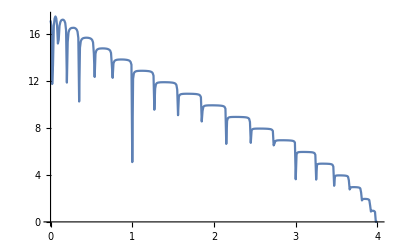

```mathematica
ListPlot[Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/2imp_sudo_Q.dat"],Joined->True]
```

```mathematica
device3[ω_,ϵ1_,m_]:=Module[{Tin=T[1,m],T1=T[1,m],μ1=RandomInteger[{1,20}], μ2=RandomInteger[{1,20}], μ3=RandomInteger[{1,20}], μ4=RandomInteger[{1,20}],μ5=RandomInteger[{1,20}], μ6=RandomInteger[{1,20}], μ7=RandomInteger[{1,20}],μ8=RandomInteger[{1,20}], μ9=RandomInteger[{1,20}], μ10=RandomInteger[{1,20}], μ11=RandomInteger[{1,20}],μ12=RandomInteger[{1,20}], μ13=RandomInteger[{1,20}], μ14=RandomInteger[{1,20}],list,b2},
imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]];
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]];
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]];
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]];
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]];
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]];
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]];
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]];
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]];
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]];
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{10,10}}->ω+ⅈ*0.0001-0]]];
b2=Module[{},list={RandomSample[{imp4,imp5,imp,imp,imp3}]};
sl1= Module[{J=SL[ω,0.0001,1,0,m]},Do[J=Inverse[IdentityMatrix[m]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,1,5}];
 J=J];
Il1:=Inverse[IdentityMatrix[m]-sl1.T1.SL[ω,0.0001,1,0,m].T1].sl1;
Ir1:=Inverse[IdentityMatrix[m]-SL[ω,0.0001,1,0,m].T1.sl1.T1].SL[ω,0.0001,1,0,m];gdd1:=Il1-ConjugateTranspose[Il1];grr1:=Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SL[ω,0.0001,1,0,m].T1.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]>tr[ω,0.0001,1,0,m],tr[ω,0.0001,1,0,m],Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]]];
b2]
```

```mathematica
Table[{ω,Mean[Table[device3[ω,0.5,20],2000]]},{ω,Range[0,4,0.01]}]
```

```mathematica
Export["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/3imp_sudo_Q.dat",%26]
```

/home/shardulmukim//PhD/fwi/sq_lattice/20sq/3imp_sudo_Q.dat

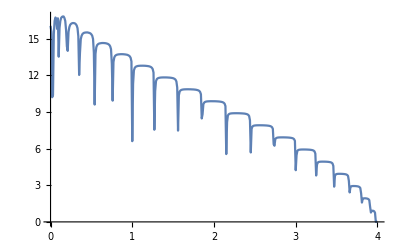

```mathematica
ListPlot[Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/3imp_sudo_Q.dat"],Joined->True]
```

```mathematica
device4[ω_,ϵ1_,m_]:=Module[{Tin=T[1,m],T1=T[1,m],μ1=RandomInteger[{1,20}], μ2=RandomInteger[{1,20}], μ3=RandomInteger[{1,20}], μ4=RandomInteger[{1,20}],μ5=RandomInteger[{1,20}], μ6=RandomInteger[{1,20}], μ7=RandomInteger[{1,20}],μ8=RandomInteger[{1,20}], μ9=RandomInteger[{1,20}], μ10=RandomInteger[{1,20}], μ11=RandomInteger[{1,20}],μ12=RandomInteger[{1,20}], μ13=RandomInteger[{1,20}], μ14=RandomInteger[{1,20}],list,b2},
imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]];
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]];
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]];
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]];
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]];
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]];
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]];
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]];
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]];
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]];
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{10,10}}->ω+ⅈ*0.0001-0]]];
b2=Module[{},list={RandomSample[{imp4,imp5,imp,imp7,imp3}]};
sl1= Module[{J=SL[ω,0.0001,1,0,m]},Do[J=Inverse[IdentityMatrix[m]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,1,5}];
 J=J];
Il1:=Inverse[IdentityMatrix[m]-sl1.T1.SL[ω,0.0001,1,0,m].T1].sl1;
Ir1:=Inverse[IdentityMatrix[m]-SL[ω,0.0001,1,0,m].T1.sl1.T1].SL[ω,0.0001,1,0,m];gdd1:=Il1-ConjugateTranspose[Il1];grr1:=Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SL[ω,0.0001,1,0,m].T1.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]>tr[ω,0.0001,1,0,m],tr[ω,0.0001,1,0,m],Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]]];
b2]
```

```mathematica
Table[{ω,Mean[Table[device4[ω,0.5,20],2000]]},{ω,Range[0,4,0.01]}]
```

```mathematica
Export["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/4imp_sudo_Q.dat",%28]
```

/home/shardulmukim//PhD/fwi/sq_lattice/20sq/4imp_sudo_Q.dat

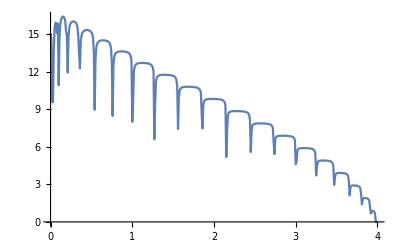

```mathematica
ListPlot[Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/4imp_sudo_Q.dat"],Joined->True]
```

```mathematica
device5[ω_,ϵ1_,m_]:=Module[{Tin=T[1,m],T1=T[1,m],μ1=RandomInteger[{1,20}], μ2=RandomInteger[{1,20}], μ3=RandomInteger[{1,20}], μ4=RandomInteger[{1,20}],μ5=RandomInteger[{1,20}], μ6=RandomInteger[{1,20}], μ7=RandomInteger[{1,20}],μ8=RandomInteger[{1,20}], μ9=RandomInteger[{1,20}], μ10=RandomInteger[{1,20}], μ11=RandomInteger[{1,20}],μ12=RandomInteger[{1,20}], μ13=RandomInteger[{1,20}], μ14=RandomInteger[{1,20}],list,b2},
imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]];
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]];
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]];
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]];
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]];
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]];
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]];
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]];
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]];
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]];
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{10,10}}->ω+ⅈ*0.0001-0]]];
b2=Module[{},list={RandomSample[{imp4,imp5,imp8,imp7,imp3}]};
sl1= Module[{J=SL[ω,0.0001,1,0,m]},Do[J=Inverse[IdentityMatrix[m]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,1,5}];
 J=J];
Il1:=Inverse[IdentityMatrix[m]-sl1.T1.SL[ω,0.0001,1,0,m].T1].sl1;
Ir1:=Inverse[IdentityMatrix[m]-SL[ω,0.0001,1,0,m].T1.sl1.T1].SL[ω,0.0001,1,0,m];gdd1:=Il1-ConjugateTranspose[Il1];grr1:=Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SL[ω,0.0001,1,0,m].T1.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]>tr[ω,0.0001,1,0,m],tr[ω,0.0001,1,0,m],Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]]];
b2]
```

```mathematica
Table[{ω,Mean[Table[device5[ω,0.5,20],2000]]},{ω,Range[0,4,0.01]}]
```

```mathematica
Export["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/5imp_sudo_Q.dat",%30]
```

/home/shardulmukim//PhD/fwi/sq_lattice/20sq/5imp_sudo_Q.dat

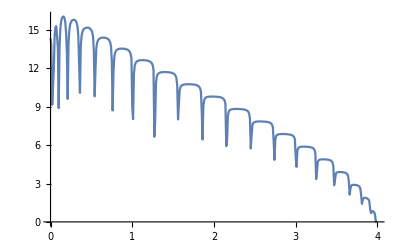

```mathematica
ListPlot[Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/5imp_sudo_Q.dat"],Joined->True]
```

```mathematica
device6[ω_,ϵ1_,m_]:=Module[{Tin=T[1,m],T1=T[1,m],μ1=RandomInteger[{1,10}], μ2=RandomInteger[{1,20}], μ3=RandomInteger[{11,20}], μ4=RandomInteger[{1,20}],μ5=RandomInteger[{1,20}], μ6=RandomInteger[{1,20}], μ7=RandomInteger[{1,20}],μ8=RandomInteger[{1,20}], μ9=RandomInteger[{1,20}], μ10=RandomInteger[{1,20}], μ11=RandomInteger[{1,20}],μ12=RandomInteger[{1,20}], μ13=RandomInteger[{1,20}], μ14=RandomInteger[{1,20}],list,b2},
imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]];
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ3,μ3},{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]];
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]];
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]];
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]];
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]];
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]];
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]];
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]];
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{10,10}}->ω+ⅈ*0.0001-0]]];
b2=Module[{},list={RandomSample[{imp4,imp5,imp8,imp7,imp3}]};
sl1= Module[{J=SL[ω,0.0001,1,0,m]},Do[J=Inverse[IdentityMatrix[m]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,1,5}];
 J=J];
Il1:=Inverse[IdentityMatrix[m]-sl1.T1.SL[ω,0.0001,1,0,m].T1].sl1;
Ir1:=Inverse[IdentityMatrix[m]-SL[ω,0.0001,1,0,m].T1.sl1.T1].SL[ω,0.0001,1,0,m];gdd1:=Il1-ConjugateTranspose[Il1];grr1:=Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SL[ω,0.0001,1,0,m].T1.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]>tr[ω,0.0001,1,0,m],tr[ω,0.0001,1,0,m],Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]]];
b2]
```

```mathematica
Export["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/6imp_sudo_Q.dat",%32]
```

/home/shardulmukim//PhD/fwi/sq_lattice/20sq/6imp_sudo_Q.dat

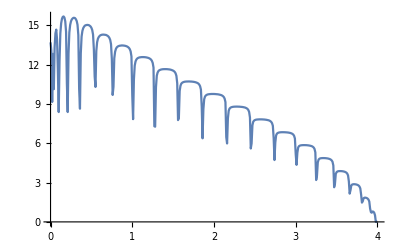

```mathematica
ListPlot[Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/6imp_sudo_Q.dat"],Joined->True]
```

```mathematica
device8[ω_,ϵ1_,m_]:=Module[{Tin=T[1,m],T1=T[1,m],μ1=RandomInteger[{1,20}], μ2=RandomInteger[{1,10}], μ3=RandomInteger[{1,10}], μ4=RandomInteger[{11,20}],μ5=RandomInteger[{1,20}], μ6=RandomInteger[{11,20}], μ7=RandomInteger[{11,20}],μ8=RandomInteger[{11,20}], μ9=RandomInteger[{1,20}], μ10=RandomInteger[{1,20}], μ11=RandomInteger[{1,20}],μ12=RandomInteger[{1,20}], μ13=RandomInteger[{1,20}], μ14=RandomInteger[{1,20}],list,b2},
imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ2,μ2},{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]];
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ3,μ3},{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ4,μ4},{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{10,10}}->ω+ⅈ*0.0001-0]]];
b2=Module[{},list={RandomSample[{imp1,imp2,imp3,imp4,imp5}]};
sl1= Module[{J=SL[ω,0.0001,1,0,m]},Do[J=Inverse[IdentityMatrix[m]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,1,5}];
 J=J];
Il1:=Inverse[IdentityMatrix[m]-sl1.T1.SL[ω,0.0001,1,0,m].T1].sl1;
Ir1:=Inverse[IdentityMatrix[m]-SL[ω,0.0001,1,0,m].T1.sl1.T1].SL[ω,0.0001,1,0,m];gdd1:=Il1-ConjugateTranspose[Il1];grr1:=Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SL[ω,0.0001,1,0,m].T1.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]>tr[ω,0.0001,1,0,m],tr[ω,0.0001,1,0,m],Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]]];
b2]
```

```mathematica
Mean[ParallelTable[device8[0,0.5,20],2000]]
```

12.8047

```mathematica
Table[{ω,Mean[ParallelTable[device8[ω,0.5,20],2000]]},{ω,Range[0,4,0.01]}]
```

{{0.,12.8991},{0.01,12.2029},{0.02,9.2329},{0.03,16.1423},{0.04,7.89395},{0.05,11.0017},{0.06,13.0033},{0.07,13.5743},{0.08,13.0083},{0.09,7.49927},{0.1,11.0949},{0.11,8.91209},{0.12,12.529},{0.13,13.9648},{0.14,14.6392},{0.15,14.9311},{0.16,15.0387},{0.17,14.9808},{0.18,14.7225},{0.19,13.9468},{0.2,7.12934},{0.21,9.72844},{0.22,9.92822},{0.23,13.0546},{0.24,14.1878},{0.25,14.6924},{0.26,14.9365},{0.27,15.0741},{0.28,15.163},{0.29,15.1625},{0.3,15.1679},{0.31,15.0855},{0.32,14.949},{0.33,14.6684},{0.34,13.9583},{0.35,7.32141},{0.36,8.74453},{0.37,10.4638},{0.38,13.1013},{0.39,13.9343},{0.4,14.3099},{0.41,14.5316},{0.42,14.6449},{0.43,14.6995},{0.44,14.7448},{0.45,14.7545},{0.46,14.765},{0.47,14.7501},{0.48,14.6973},{0.49,14.6475},{0.5,14.5435},{0.51,14.3559},{0.52,14.0339},{0.53,13.0442},{0.54,9.42119},{0.55,7.76843},{0.56,11.4232},{0.57,13.0132},{0.58,13.5181},{0.59,13.7896},{0.6,13.9245},{0.61,13.9935},{0.62,14.0463},{0.63,14.0714},{0.64,14.0959},{0.65,14.0998},{0.66,14.1034},{0.67,14.0914},{0.68,14.0777},{0.69,14.036},{0.7,13.9986},{0.71,13.926},{0.72,13.8203},{0.73,13.6588},{0.74,13.3403},{0.75,12.3676},{0.76,9.27519},{0.77,7.67245},{0.78,11.2474},{0.79,12.4517},{0.8,12.8611},{0.81,13.0497},{0.82,13.1595},{0.83,13.2263},{0.84,13.2636},{0.85,13.2856},{0.86,13.3032},{0.87,13.3154},{0.88,13.3155},{0.89,13.3156},{0.9,13.3102},{0.91,13.3002},{0.92,13.2767},{0.93,13.2531},{0.94,13.2178},{0.95,13.1686},{0.96,13.1009},{0.97,12.9886},{0.98,12.8171},{0.99,12.4491},{1.,10.5025},{1.01,8.78097},{1.02,8.41399},{1.03,11.1598},{1.04,11.8762},{1.05,12.1357},{1.06,12.2689},{1.07,12.3499},{1.08,12.3977},{1.09,12.4232},{1.1,12.4432},{1.11,12.4537},{1.12,12.4609},{1.13,12.4648},{1.14,12.4656},{1.15,12.4586},{1.16,12.4531},{1.17,12.4464},{1.18,12.4285},{1.19,12.4082},{1.2,12.3834},{1.21,12.3515},{1.22,12.3052},{1.23,12.2338},{1.24,12.1396},{1.25,11.9736},{1.26,11.6042},{1.27,8.79298},{1.28,7.76748},{1.29,8.41408},{1.3,10.5359},{1.31,11.0829},{1.32,11.3107},{1.33,11.4137},{1.34,11.4745},{1.35,11.511},{1.36,11.5316},{1.37,11.5459},{1.38,11.5593},{1.39,11.5626},{1.4,11.5673},{1.41,11.5682},{1.42,11.5649},{1.43,11.5622},{1.44,11.5559},{1.45,11.5449},{1.46,11.5344},{1.47,11.5192},{1.48,11.4965},{1.49,11.4675},{1.5,11.4304},{1.51,11.3831},{1.52,11.3121},{1.53,11.1994},{1.54,10.9909},{1.55,10.4618},{1.56,6.32327},{1.57,6.54725},{1.58,8.9624},{1.59,10.0154},{1.6,10.3374},{1.61,10.4681},{1.62,10.5374},{1.63,10.5803},{1.64,10.6024},{1.65,10.6207},{1.66,10.6302},{1.67,10.64},{1.68,10.6406},{1.69,10.6439},{1.7,10.6426},{1.71,10.6398},{1.72,10.6375},{1.73,10.6295},{1.74,10.6189},{1.75,10.6087},{1.76,10.5981},{1.77,10.5793},{1.78,10.5594},{1.79,10.528},{1.8,10.4927},{1.81,10.4353},{1.82,10.3515},{1.83,10.2237},{1.84,9.95924},{1.85,8.92193},{1.86,6.5507},{1.87,6.83984},{1.88,8.84534},{1.89,9.32553},{1.9,9.49955},{1.91,9.58575},{1.92,9.6292},{1.93,9.654},{1.94,9.67034},{1.95,9.68547},{1.96,9.69216},{1.97,9.69782},{1.98,9.69845},{1.99,9.69797},{2.,9.69608},{2.01,9.6943},{2.02,9.68878},{2.03,9.68484},{2.04,9.67358},{2.05,9.66397},{2.06,9.65323},{2.07,9.63564},{2.08,9.61297},{2.09,9.58628},{2.1,9.54793},{2.11,9.49342},{2.12,9.41304},{2.13,9.2826},{2.14,9.01267},{2.15,7.36227},{2.16,6.0322},{2.17,6.63289},{2.18,8.0487},{2.19,8.44491},{2.2,8.58782},{2.21,8.65056},{2.22,8.6894},{2.23,8.71014},{2.24,8.7267},{2.25,8.73524},{2.26,8.74063},{2.27,8.74141},{2.28,8.74566},{2.29,8.74411},{2.3,8.74184},{2.31,8.73924},{2.32,8.73516},{2.33,8.72747},{2.34,8.71625},{2.35,8.7063},{2.36,8.69361},{2.37,8.6768},{2.38,8.65316},{2.39,8.62373},{2.4,8.58557},{2.41,8.52728},{2.42,8.43258},{2.43,8.26974},{2.44,7.86511},{2.45,4.85858},{2.46,5.07206},{2.47,6.67576},{2.48,7.40959},{2.49,7.59925},{2.5,7.6845},{2.51,7.72026},{2.52,7.74475},{2.53,7.75943},{2.54,7.76805},{2.55,7.77451},{2.56,7.77671},{2.57,7.77836},{2.58,7.77807},{2.59,7.7748},{2.6,7.77046},{2.61,7.76574},{2.62,7.75881},{2.63,7.7514},{2.64,7.73976},{2.65,7.72447},{2.66,7.70585},{2.67,7.68299},{2.68,7.6514},{2.69,7.6053},{2.7,7.54135},{2.71,7.43041},{2.72,7.20789},{2.73,6.46567},{2.74,4.75504},{2.75,5.01985},{2.76,6.25632},{2.77,6.5785},{2.78,6.69414},{2.79,6.74222},{2.8,6.77059},{2.81,6.78558},{2.82,6.79542},{2.83,6.80045},{2.84,6.80426},{2.85,6.80264},{2.86,6.79989},{2.87,6.79929},{2.88,6.79347},{2.89,6.78606},{2.9,6.78008},{2.91,6.76678},{2.92,6.75381},{2.93,6.73782},{2.94,6.71407},{2.95,6.68245},{2.96,6.63749},{2.97,6.57442},{2.98,6.46795},{2.99,6.24957},{3.,5.37953},{3.01,4.27726},{3.02,4.32732},{3.03,5.40886},{3.04,5.65493},{3.05,5.73892},{3.06,5.77901},{3.07,5.79839},{3.08,5.81189},{3.09,5.81582},{3.1,5.81905},{3.11,5.81863},{3.12,5.81744},{3.13,5.81293},{3.14,5.80731},{3.15,5.79945},{3.16,5.78998},{3.17,5.7773},{3.18,5.75706},{3.19,5.73319},{3.2,5.70297},{3.21,5.65767},{3.22,5.5833},{3.23,5.46107},{3.24,5.1871},{3.25,3.41503},{3.26,3.41363},{3.27,3.98244},{3.28,4.58248},{3.29,4.73133},{3.3,4.78599},{3.31,4.81169},{3.32,4.82398},{3.33,4.83145},{3.34,4.83094},{3.35,4.83174},{3.36,4.82633},{3.37,4.81914},{3.38,4.8105},{3.39,4.79928},{3.4,4.7797},{3.41,4.75782},{3.42,4.72691},{3.43,4.67978},{3.44,4.60649},{3.45,4.48524},{3.46,4.19549},{3.47,2.6422},{3.48,2.77403},{3.49,3.20984},{3.5,3.66189},{3.51,3.76923},{3.52,3.81664},{3.53,3.83088},{3.54,3.83882},{3.55,3.83797},{3.56,3.83394},{3.57,3.828},{3.58,3.81522},{3.59,3.79693},{3.6,3.77456},{3.61,3.73805},{3.62,3.68175},{3.63,3.59978},{3.64,3.44826},{3.65,3.01601},{3.66,2.04895},{3.67,2.05854},{3.68,2.54864},{3.69,2.75941},{3.7,2.81436},{3.71,2.82589},{3.72,2.83087},{3.73,2.82345},{3.74,2.80802},{3.75,2.78608},{3.76,2.74801},{3.77,2.69744},{3.78,2.61276},{3.79,2.45454},{3.8,2.0058},{3.81,1.41019},{3.82,1.35818},{3.83,1.62952},{3.84,1.7619},{3.85,1.78305},{3.86,1.77379},{3.87,1.74382},{3.88,1.69221},{3.89,1.60299},{3.9,1.43589},{3.91,0.951505},{3.92,0.72498},{3.93,0.61458},{3.94,0.656684},{3.95,0.672941},{3.96,0.600244},{3.97,0.39125},{3.98,0.000456674},{3.99,0.0000168049},{4.,5.34708×10^-6}}

```mathematica
Export["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/8imp_sudo_Q.dat",%31]
```

/home/shardulmukim//PhD/fwi/sq_lattice/20sq/8imp_sudo_Q.dat

```mathematica
Export["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/7imp_sudo_Q.dat",%75]
```

/home/shardulmukim//PhD/fwi/sq_lattice/20sq/7imp_sudo_Q.dat

```mathematica
device9[ω_,ϵ1_,m_]:=Module[{Tin=T[1,m],T1=T[1,m],μ1=RandomInteger[{1,20}], μ2=RandomInteger[{1,10}], μ3=RandomInteger[{1,10}], μ4=RandomInteger[{11,20}],μ5=RandomInteger[{1,10}], μ6=RandomInteger[{11,20}], μ7=RandomInteger[{11,20}],μ8=RandomInteger[{11,20}], μ9=RandomInteger[{11,20}], μ10=RandomInteger[{1,20}], μ11=RandomInteger[{1,20}],μ12=RandomInteger[{1,20}], μ13=RandomInteger[{1,20}], μ14=RandomInteger[{1,20}],list,b2},
imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ2,μ2},{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]];
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ3,μ3},{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ4,μ4},{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ5,μ5},{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]];
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{10,10}}->ω+ⅈ*0.0001-0]]];
b2=Module[{},list={RandomSample[{imp1,imp2,imp3,imp4,imp5}]};
sl1= Module[{J=SL[ω,0.0001,1,0,m]},Do[J=Inverse[IdentityMatrix[m]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,1,5}];
 J=J];
Il1:=Inverse[IdentityMatrix[m]-sl1.T1.SL[ω,0.0001,1,0,m].T1].sl1;
Ir1:=Inverse[IdentityMatrix[m]-SL[ω,0.0001,1,0,m].T1.sl1.T1].SL[ω,0.0001,1,0,m];gdd1:=Il1-ConjugateTranspose[Il1];grr1:=Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SL[ω,0.0001,1,0,m].T1.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]>tr[ω,0.0001,1,0,m],tr[ω,0.0001,1,0,m],Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]]];
b2]
```

```mathematica
Mean[ParallelTable[device9[0,0.5,20],2000]]
```

12.4457

```mathematica
Export["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/9imp_sudo_Q.dat",%32]
```

/home/shardulmukim//PhD/fwi/sq_lattice/20sq/9imp_sudo_Q.dat

```mathematica
Table[{ω,Mean[ParallelTable[device9[ω,0.5,20],2000]]},{ω,Range[0,4,0.01]}]
```

{{0.,12.4779},{0.01,11.9739},{0.02,9.15251},{0.03,16.7164},{0.04,8.09539},{0.05,9.5133},{0.06,12.0569},{0.07,12.8872},{0.08,12.5723},{0.09,6.61888},{0.1,12.6134},{0.11,7.74385},{0.12,11.3038},{0.13,13.3345},{0.14,14.1292},{0.15,14.5379},{0.16,14.6553},{0.17,14.6974},{0.18,14.4622},{0.19,13.7056},{0.2,6.88965},{0.21,11.0718},{0.22,8.26466},{0.23,12.0259},{0.24,13.5887},{0.25,14.2549},{0.26,14.6245},{0.27,14.8068},{0.28,14.9038},{0.29,14.9652},{0.3,14.9573},{0.31,14.8733},{0.32,14.7618},{0.33,14.4702},{0.34,13.7837},{0.35,7.1465},{0.36,9.32442},{0.37,8.87552},{0.38,12.2071},{0.39,13.5203},{0.4,14.0587},{0.41,14.3037},{0.42,14.455},{0.43,14.5372},{0.44,14.5913},{0.45,14.6199},{0.46,14.6156},{0.47,14.6038},{0.48,14.5732},{0.49,14.4992},{0.5,14.4088},{0.51,14.2187},{0.52,13.8926},{0.53,12.9676},{0.54,8.30628},{0.55,7.59719},{0.56,10.2334},{0.57,12.5048},{0.58,13.2454},{0.59,13.584},{0.6,13.7476},{0.61,13.8526},{0.62,13.9178},{0.63,13.9568},{0.64,13.986},{0.65,13.9883},{0.66,13.9964},{0.67,13.9832},{0.68,13.9637},{0.69,13.936},{0.7,13.887},{0.71,13.8299},{0.72,13.7148},{0.73,13.5507},{0.74,13.221},{0.75,12.3423},{0.76,8.2291},{0.77,7.43503},{0.78,10.1185},{0.79,12.0456},{0.8,12.6336},{0.81,12.8969},{0.82,13.0325},{0.83,13.1153},{0.84,13.1626},{0.85,13.1993},{0.86,13.2254},{0.87,13.2273},{0.88,13.2346},{0.89,13.2333},{0.9,13.2291},{0.91,13.2166},{0.92,13.2008},{0.93,13.1736},{0.94,13.134},{0.95,13.0825},{0.96,13.0117},{0.97,12.8931},{0.98,12.7157},{0.99,12.3458},{1.,10.6993},{1.01,8.31419},{1.02,7.40499},{1.03,10.4775},{1.04,11.596},{1.05,11.9889},{1.06,12.1474},{1.07,12.2475},{1.08,12.3081},{1.09,12.3472},{1.1,12.3687},{1.11,12.3842},{1.12,12.3973},{1.13,12.4013},{1.14,12.4026},{1.15,12.3962},{1.16,12.3976},{1.17,12.3826},{1.18,12.3668},{1.19,12.3515},{1.2,12.3184},{1.21,12.2833},{1.22,12.234},{1.23,12.166},{1.24,12.0558},{1.25,11.8853},{1.26,11.5256},{1.27,9.27615},{1.28,7.6553},{1.29,7.3883},{1.3,9.96498},{1.31,10.8461},{1.32,11.1766},{1.33,11.3225},{1.34,11.3901},{1.35,11.4436},{1.36,11.475},{1.37,11.4929},{1.38,11.5056},{1.39,11.5161},{1.4,11.5187},{1.41,11.5181},{1.42,11.5175},{1.43,11.5141},{1.44,11.5091},{1.45,11.4999},{1.46,11.481},{1.47,11.4661},{1.48,11.4449},{1.49,11.4166},{1.5,11.3763},{1.51,11.3233},{1.52,11.2444},{1.53,11.1264},{1.54,10.919},{1.55,10.4201},{1.56,6.25584},{1.57,6.51715},{1.58,8.19044},{1.59,9.72721},{1.6,10.1798},{1.61,10.3728},{1.62,10.4664},{1.63,10.5213},{1.64,10.5515},{1.65,10.5701},{1.66,10.5847},{1.67,10.5939},{1.68,10.5984},{1.69,10.6028},{1.7,10.6052},{1.71,10.6006},{1.72,10.5975},{1.73,10.5905},{1.74,10.5805},{1.75,10.5681},{1.76,10.5562},{1.77,10.5384},{1.78,10.5136},{1.79,10.4802},{1.8,10.4418},{1.81,10.3812},{1.82,10.2977},{1.83,10.1602},{1.84,9.88958},{1.85,8.98637},{1.86,6.10293},{1.87,6.02359},{1.88,8.41991},{1.89,9.16112},{1.9,9.3917},{1.91,9.50934},{1.92,9.57226},{1.93,9.61196},{1.94,9.63269},{1.95,9.64663},{1.96,9.65913},{1.97,9.66343},{1.98,9.66534},{1.99,9.66589},{2.,9.66581},{2.01,9.66448},{2.02,9.65791},{2.03,9.65237},{2.04,9.63951},{2.05,9.63224},{2.06,9.61564},{2.07,9.60095},{2.08,9.57576},{2.09,9.54714},{2.1,9.50745},{2.11,9.45204},{2.12,9.36309},{2.13,9.22303},{2.14,8.95159},{2.15,7.60391},{2.16,5.94631},{2.17,5.93061},{2.18,7.62678},{2.19,8.30426},{2.2,8.50339},{2.21,8.59914},{2.22,8.64537},{2.23,8.6737},{2.24,8.69472},{2.25,8.70549},{2.26,8.71279},{2.27,8.7165},{2.28,8.71844},{2.29,8.71748},{2.3,8.7147},{2.31,8.71325},{2.32,8.70675},{2.33,8.70088},{2.34,8.68921},{2.35,8.67741},{2.36,8.6629},{2.37,8.64434},{2.38,8.6178},{2.39,8.58849},{2.4,8.54094},{2.41,8.48022},{2.42,8.38554},{2.43,8.21096},{2.44,7.82039},{2.45,4.97546},{2.46,5.23206},{2.47,6.0681},{2.48,7.20938},{2.49,7.51331},{2.5,7.62383},{2.51,7.68463},{2.52,7.71327},{2.53,7.73024},{2.54,7.74261},{2.55,7.74949},{2.56,7.7539},{2.57,7.75656},{2.58,7.75329},{2.59,7.75202},{2.6,7.74949},{2.61,7.74448},{2.62,7.73698},{2.63,7.72765},{2.64,7.71493},{2.65,7.69916},{2.66,7.67984},{2.67,7.65298},{2.68,7.61473},{2.69,7.57074},{2.7,7.49996},{2.71,7.38405},{2.72,7.15711},{2.73,6.48371},{2.74,4.54685},{2.75,4.65031},{2.76,5.95485},{2.77,6.48115},{2.78,6.6318},{2.79,6.7072},{2.8,6.74132},{2.81,6.7593},{2.82,6.77246},{2.83,6.77835},{2.84,6.78187},{2.85,6.78308},{2.86,6.7803},{2.87,6.77794},{2.88,6.77191},{2.89,6.76575},{2.9,6.75707},{2.91,6.74719},{2.92,6.72918},{2.93,6.71188},{2.94,6.68828},{2.95,6.65051},{2.96,6.60413},{2.97,6.53613},{2.98,6.4218},{2.99,6.20391},{3.,5.43183},{3.01,3.99336},{3.02,3.99772},{3.03,5.17216},{3.04,5.56294},{3.05,5.69341},{3.06,5.74487},{3.07,5.77375},{3.08,5.79041},{3.09,5.79698},{3.1,5.80064},{3.11,5.80144},{3.12,5.80046},{3.13,5.79584},{3.14,5.78912},{3.15,5.77886},{3.16,5.76986},{3.17,5.75207},{3.18,5.7346},{3.19,5.70624},{3.2,5.67092},{3.21,5.62184},{3.22,5.54535},{3.23,5.41781},{3.24,5.14543},{3.25,3.72282},{3.26,3.47719},{3.27,3.61329},{3.28,4.42728},{3.29,4.67576},{3.3,4.75433},{3.31,4.78926},{3.32,4.80437},{3.33,4.81347},{3.34,4.81518},{3.35,4.81512},{3.36,4.81197},{3.37,4.80572},{3.38,4.79383},{3.39,4.77825},{3.4,4.75713},{3.41,4.73619},{3.42,4.70105},{3.43,4.65146},{3.44,4.57191},{3.45,4.43675},{3.46,4.15812},{3.47,2.81504},{3.48,2.83646},{3.49,2.9632},{3.5,3.55219},{3.51,3.72517},{3.52,3.79289},{3.53,3.81255},{3.54,3.82193},{3.55,3.82313},{3.56,3.81919},{3.57,3.81065},{3.58,3.79935},{3.59,3.77787},{3.6,3.75022},{3.61,3.71045},{3.62,3.65497},{3.63,3.56294},{3.64,3.4013},{3.65,2.99635},{3.66,2.04276},{3.67,2.07301},{3.68,2.38489},{3.69,2.70235},{3.7,2.78665},{3.71,2.80929},{3.72,2.81372},{3.73,2.80805},{3.74,2.79002},{3.75,2.76438},{3.76,2.72736},{3.77,2.6689},{3.78,2.57353},{3.79,2.40412},{3.8,1.98625},{3.81,1.30863},{3.82,1.35798},{3.83,1.5208},{3.84,1.71041},{3.85,1.7477},{3.86,1.74833},{3.87,1.71464},{3.88,1.6587},{3.89,1.5624},{3.9,1.38481},{3.91,0.933482},{3.92,0.666929},{3.93,0.654473},{3.94,0.604137},{3.95,0.631627},{3.96,0.558117},{3.97,0.350333},{3.98,0.000456674},{3.99,0.0000168049},{4.,5.34708×10^-6}}

```mathematica
device10[ω_,ϵ1_,m_]:=Module[{Tin=T[1,m],T1=T[1,m],μ1=RandomInteger[{1,10}], μ2=RandomInteger[{1,10}], μ3=RandomInteger[{1,10}], μ4=RandomInteger[{11,20}],μ5=RandomInteger[{1,10}], μ6=RandomInteger[{11,20}], μ7=RandomInteger[{11,20}],μ8=RandomInteger[{11,20}], μ9=RandomInteger[{11,20}], μ10=RandomInteger[{11,20}], μ11=RandomInteger[{1,20}],μ12=RandomInteger[{1,20}], μ13=RandomInteger[{1,20}], μ14=RandomInteger[{1,20}],list,b2},
imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ1,μ1},{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]];
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ2,μ2},{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]];
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ3,μ3},{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ4,μ4},{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ5,μ5},{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]];
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{10,10}}->ω+ⅈ*0.0001-0]]];
b2=Module[{},list={RandomSample[{imp1,imp2,imp3,imp4,imp5}]};
sl1= Module[{J=SL[ω,0.0001,1,0,m]},Do[J=Inverse[IdentityMatrix[m]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,1,5}];
 J=J];
Il1:=Inverse[IdentityMatrix[m]-sl1.T1.SL[ω,0.0001,1,0,m].T1].sl1;
Ir1:=Inverse[IdentityMatrix[m]-SL[ω,0.0001,1,0,m].T1.sl1.T1].SL[ω,0.0001,1,0,m];gdd1:=Il1-ConjugateTranspose[Il1];grr1:=Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SL[ω,0.0001,1,0,m].T1.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]>tr[ω,0.0001,1,0,m],tr[ω,0.0001,1,0,m],Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]]];
b2]
```

```mathematica
Mean[ParallelTable[device10[0,0.5,20],2000]]
```

12.0381

```mathematica
Export["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/10imp_sudo_Q.dat",%33]
```

/home/shardulmukim//PhD/fwi/sq_lattice/20sq/10imp_sudo_Q.dat

```mathematica
Table[{ω,Mean[ParallelTable[device10[ω,0.5,20],2000]]},{ω,Range[0,4,0.01]}]
```

{{0.,12.0678},{0.01,11.6246},{0.02,9.19674},{0.03,16.2636},{0.04,9.33043},{0.05,8.04955},{0.06,11.0074},{0.07,12.1468},{0.08,12.0763},{0.09,6.39173},{0.1,13.6798},{0.11,7.18806},{0.12,9.9617},{0.13,12.4557},{0.14,13.5639},{0.15,14.0964},{0.16,14.3459},{0.17,14.3631},{0.18,14.1165},{0.19,13.4986},{0.2,7.16234},{0.21,11.6021},{0.22,7.13252},{0.23,10.9234},{0.24,12.9578},{0.25,13.8466},{0.26,14.2952},{0.27,14.5432},{0.28,14.6614},{0.29,14.7517},{0.3,14.7454},{0.31,14.6861},{0.32,14.5669},{0.33,14.2764},{0.34,13.6716},{0.35,7.64658},{0.36,9.6065},{0.37,7.47106},{0.38,11.2516},{0.39,13.0292},{0.4,13.6726},{0.41,14.0497},{0.42,14.2403},{0.43,14.3541},{0.44,14.4127},{0.45,14.4528},{0.46,14.4719},{0.47,14.4642},{0.48,14.4338},{0.49,14.3532},{0.5,14.2538},{0.51,14.086},{0.52,13.7632},{0.53,12.8985},{0.54,7.39404},{0.55,7.7476},{0.56,8.7218},{0.57,11.7822},{0.58,12.879},{0.59,13.3287},{0.6,13.5835},{0.61,13.7135},{0.62,13.7991},{0.63,13.8515},{0.64,13.866},{0.65,13.8863},{0.66,13.895},{0.67,13.8829},{0.68,13.866},{0.69,13.8341},{0.7,13.7887},{0.71,13.717},{0.72,13.6059},{0.73,13.4226},{0.74,13.1338},{0.75,12.2943},{0.76,7.15564},{0.77,7.13825},{0.78,9.08437},{0.79,11.4977},{0.8,12.3552},{0.81,12.7243},{0.82,12.8913},{0.83,13.0039},{0.84,13.0634},{0.85,13.108},{0.86,13.1345},{0.87,13.1513},{0.88,13.1655},{0.89,13.161},{0.9,13.1521},{0.91,13.1412},{0.92,13.1243},{0.93,13.0972},{0.94,13.0609},{0.95,13.0094},{0.96,12.9275},{0.97,12.8103},{0.98,12.6293},{0.99,12.2739},{1.,10.8412},{1.01,7.45846},{1.02,6.76565},{1.03,9.5745},{1.04,11.2295},{1.05,11.7772},{1.06,12.0166},{1.07,12.153},{1.08,12.2265},{1.09,12.2723},{1.1,12.3029},{1.11,12.3245},{1.12,12.3366},{1.13,12.339},{1.14,12.3408},{1.15,12.3449},{1.16,12.3347},{1.17,12.3241},{1.18,12.3126},{1.19,12.2885},{1.2,12.2584},{1.21,12.2192},{1.22,12.1745},{1.23,12.0999},{1.24,11.985},{1.25,11.8091},{1.26,11.4637},{1.27,9.65287},{1.28,7.25915},{1.29,6.70667},{1.3,9.24564},{1.31,10.5117},{1.32,11.0119},{1.33,11.2136},{1.34,11.3112},{1.35,11.377},{1.36,11.4098},{1.37,11.4387},{1.38,11.4584},{1.39,11.4681},{1.4,11.4696},{1.41,11.4735},{1.42,11.4721},{1.43,11.4655},{1.44,11.4603},{1.45,11.4527},{1.46,11.4389},{1.47,11.4212},{1.48,11.3964},{1.49,11.3663},{1.5,11.3282},{1.51,11.2681},{1.52,11.1904},{1.53,11.0648},{1.54,10.854},{1.55,10.3754},{1.56,6.55048},{1.57,6.68837},{1.58,7.0871},{1.59,9.30907},{1.6,10.0042},{1.61,10.2618},{1.62,10.3792},{1.63,10.4545},{1.64,10.5006},{1.65,10.5271},{1.66,10.547},{1.67,10.5525},{1.68,10.56},{1.69,10.5636},{1.7,10.5672},{1.71,10.5658},{1.72,10.5587},{1.73,10.5534},{1.74,10.5427},{1.75,10.5331},{1.76,10.5175},{1.77,10.4952},{1.78,10.4732},{1.79,10.4416},{1.8,10.3955},{1.81,10.3331},{1.82,10.2413},{1.83,10.1005},{1.84,9.83357},{1.85,9.02008},{1.86,5.87037},{1.87,5.7206},{1.88,7.7329},{1.89,8.91405},{1.9,9.27693},{1.91,9.4367},{1.92,9.51159},{1.93,9.55927},{1.94,9.5915},{1.95,9.61009},{1.96,9.62104},{1.97,9.62817},{1.98,9.63532},{1.99,9.63624},{2.,9.63472},{2.01,9.63136},{2.02,9.62714},{2.03,9.62022},{2.04,9.60984},{2.05,9.59974},{2.06,9.5831},{2.07,9.56357},{2.08,9.53852},{2.09,9.50757},{2.1,9.46377},{2.11,9.40284},{2.12,9.3164},{2.13,9.18054},{2.14,8.90358},{2.15,7.79904},{2.16,5.57978},{2.17,5.42339},{2.18,7.0895},{2.19,8.10755},{2.2,8.41015},{2.21,8.53446},{2.22,8.59885},{2.23,8.63482},{2.24,8.66026},{2.25,8.67588},{2.26,8.6861},{2.27,8.69024},{2.28,8.69174},{2.29,8.69039},{2.3,8.68984},{2.31,8.68615},{2.32,8.67928},{2.33,8.67287},{2.34,8.66189},{2.35,8.65297},{2.36,8.63418},{2.37,8.61357},{2.38,8.58699},{2.39,8.55397},{2.4,8.50531},{2.41,8.44381},{2.42,8.34032},{2.43,8.16261},{2.44,7.79045},{2.45,5.24905},{2.46,5.19633},{2.47,5.4633},{2.48,6.91324},{2.49,7.40644},{2.5,7.56322},{2.51,7.63638},{2.52,7.67794},{2.53,7.70239},{2.54,7.71767},{2.55,7.72556},{2.56,7.73153},{2.57,7.73324},{2.58,7.73259},{2.59,7.73065},{2.6,7.72604},{2.61,7.72148},{2.62,7.71417},{2.63,7.70605},{2.64,7.69007},{2.65,7.67228},{2.66,7.65124},{2.67,7.62338},{2.68,7.5851},{2.69,7.53443},{2.7,7.46099},{2.71,7.33791},{2.72,7.1207},{2.73,6.51064},{2.74,4.43119},{2.75,4.50519},{2.76,5.48934},{2.77,6.31266},{2.78,6.56739},{2.79,6.66215},{2.8,6.7079},{2.81,6.73397},{2.82,6.74994},{2.83,6.75847},{2.84,6.76123},{2.85,6.76514},{2.86,6.76293},{2.87,6.76027},{2.88,6.75375},{2.89,6.74632},{2.9,6.73884},{2.91,6.7277},{2.92,6.70944},{2.93,6.68866},{2.94,6.6622},{2.95,6.62244},{2.96,6.57054},{2.97,6.49764},{2.98,6.38376},{2.99,6.16294},{3.,5.47827},{3.01,3.76279},{3.02,3.9714},{3.03,4.75772},{3.04,5.46393},{3.05,5.63613},{3.06,5.70919},{3.07,5.74824},{3.08,5.76794},{3.09,5.7771},{3.1,5.7828},{3.11,5.78739},{3.12,5.78312},{3.13,5.77938},{3.14,5.77264},{3.15,5.76409},{3.16,5.75136},{3.17,5.73388},{3.18,5.7136},{3.19,5.68417},{3.2,5.64569},{3.21,5.59347},{3.22,5.51099},{3.23,5.37652},{3.24,5.10877},{3.25,3.95078},{3.26,3.45426},{3.27,3.46458},{3.28,4.20933},{3.29,4.59993},{3.3,4.71641},{3.31,4.76246},{3.32,4.78352},{3.33,4.79618},{3.34,4.80037},{3.35,4.79913},{3.36,4.79677},{3.37,4.7876},{3.38,4.77774},{3.39,4.76155},{3.4,4.74035},{3.41,4.7145},{3.42,4.67632},{3.43,4.62037},{3.44,4.54224},{3.45,4.40526},{3.46,4.12368},{3.47,3.02742},{3.48,2.76774},{3.49,2.77614},{3.5,3.36468},{3.51,3.6647},{3.52,3.76311},{3.53,3.78989},{3.54,3.80589},{3.55,3.80983},{3.56,3.80497},{3.57,3.79809},{3.58,3.78412},{3.59,3.76123},{3.6,3.73463},{3.61,3.69109},{3.62,3.63118},{3.63,3.53287},{3.64,3.3639},{3.65,2.97804},{3.66,2.01632},{3.67,2.13579},{3.68,2.2201},{3.69,2.61522},{3.7,2.74368},{3.71,2.78896},{3.72,2.7958},{3.73,2.78765},{3.74,2.77419},{3.75,2.74639},{3.76,2.70257},{3.77,2.64012},{3.78,2.5426},{3.79,2.37214},{3.8,1.97476},{3.81,1.31834},{3.82,1.38527},{3.83,1.41207},{3.84,1.63978},{3.85,1.71522},{3.86,1.72011},{3.87,1.68641},{3.88,1.62716},{3.89,1.52416},{3.9,1.33891},{3.91,0.918125},{3.92,0.626448},{3.93,0.697384},{3.94,0.571982},{3.95,0.587762},{3.96,0.516612},{3.97,0.317461},{3.98,0.000456674},{3.99,0.0000168049},{4.,5.34708×10^-6}}

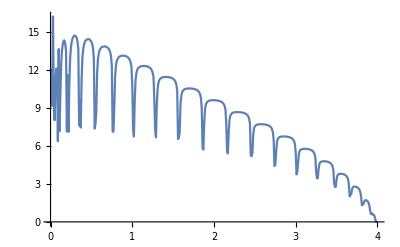

```mathematica
ListPlot[%33,Joined->True]
```

```mathematica
device11[ω_,ϵ1_,m_]:=Module[{Tin=T[1,m],T1=T[1,m],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,10}], μ3=RandomInteger[{1,10}], μ4=RandomInteger[{11,20}],μ5=RandomInteger[{1,10}], μ6=RandomInteger[{11,20}], μ7=RandomInteger[{11,20}],μ8=RandomInteger[{11,20}], μ9=RandomInteger[{11,20}], μ10=RandomInteger[{8,14}], μ11=RandomInteger[{15,20}],μ12=RandomInteger[{1,20}], μ13=RandomInteger[{1,20}], μ14=RandomInteger[{1,20}],list,b2},
imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ1,μ1},{μ10,μ10},{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]];
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ2,μ2},{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]];
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ3,μ3},{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ4,μ4},{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ5,μ5},{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]];
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{10,10}}->ω+ⅈ*0.0001-0]]];
b2=Module[{},list={RandomSample[{imp1,imp2,imp3,imp4,imp5}]};
sl1= Module[{J=SL[ω,0.0001,1,0,m]},Do[J=Inverse[IdentityMatrix[m]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,1,5}];
 J=J];
Il1:=Inverse[IdentityMatrix[m]-sl1.T1.SL[ω,0.0001,1,0,m].T1].sl1;
Ir1:=Inverse[IdentityMatrix[m]-SL[ω,0.0001,1,0,m].T1.sl1.T1].SL[ω,0.0001,1,0,m];gdd1:=Il1-ConjugateTranspose[Il1];grr1:=Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SL[ω,0.0001,1,0,m].T1.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]>tr[ω,0.0001,1,0,m],tr[ω,0.0001,1,0,m],Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]]];
b2]
```

```mathematica
Mean[ParallelTable[device11[0,0.5,20],2000]]
```

11.7497

```mathematica
Export["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/11imp_sudo_Q.dat",%34]
```

/home/shardulmukim//PhD/fwi/sq_lattice/20sq/11imp_sudo_Q.dat

```mathematica
Table[{ω,Mean[ParallelTable[device11[ω,0.5,20],2000]]},{ω,Range[0,4,0.01]}]
```

{{0.,11.81},{0.01,11.3898},{0.02,9.10923},{0.03,15.7364},{0.04,10.8882},{0.05,7.22458},{0.06,9.79935},{0.07,11.5829},{0.08,11.6064},{0.09,6.40427},{0.1,13.716},{0.11,7.27245},{0.12,8.57767},{0.13,11.5428},{0.14,12.9653},{0.15,13.5463},{0.16,13.8616},{0.17,13.9795},{0.18,13.8568},{0.19,13.245},{0.2,7.57701},{0.21,10.9451},{0.22,7.07089},{0.23,9.52287},{0.24,12.2201},{0.25,13.3425},{0.26,13.9591},{0.27,14.2454},{0.28,14.4479},{0.29,14.5143},{0.3,14.534},{0.31,14.493},{0.32,14.3666},{0.33,14.1237},{0.34,13.5231},{0.35,8.34347},{0.36,9.40202},{0.37,6.70268},{0.38,10.0074},{0.39,12.4226},{0.4,13.3579},{0.41,13.8058},{0.42,14.0295},{0.43,14.1771},{0.44,14.2682},{0.45,14.3101},{0.46,14.3479},{0.47,14.3116},{0.48,14.2934},{0.49,14.2538},{0.5,14.1366},{0.51,13.9564},{0.52,13.6497},{0.53,12.8747},{0.54,6.93716},{0.55,7.95579},{0.56,7.6821},{0.57,10.9926},{0.58,12.4492},{0.59,13.0789},{0.6,13.3944},{0.61,13.545},{0.62,13.6563},{0.63,13.7146},{0.64,13.7645},{0.65,13.7786},{0.66,13.7879},{0.67,13.7806},{0.68,13.7629},{0.69,13.7414},{0.7,13.6905},{0.71,13.622},{0.72,13.5089},{0.73,13.3431},{0.74,13.0365},{0.75,12.2715},{0.76,6.89684},{0.77,7.2892},{0.78,7.84324},{0.79,10.7746},{0.8,12.0094},{0.81,12.4959},{0.82,12.7497},{0.83,12.8866},{0.84,12.9593},{0.85,13.0177},{0.86,13.0446},{0.87,13.0678},{0.88,13.08},{0.89,13.084},{0.9,13.0741},{0.91,13.0653},{0.92,13.049},{0.93,13.0212},{0.94,12.9875},{0.95,12.928},{0.96,12.8474},{0.97,12.7373},{0.98,12.5526},{0.99,12.2011},{1.,10.9694},{1.01,6.90368},{1.02,6.78875},{1.03,8.36227},{1.04,10.7612},{1.05,11.5421},{1.06,11.8625},{1.07,12.0311},{1.08,12.1269},{1.09,12.1841},{1.1,12.2313},{1.11,12.2524},{1.12,12.2737},{1.13,12.2822},{1.14,12.2884},{1.15,12.2828},{1.16,12.2769},{1.17,12.2642},{1.18,12.2489},{1.19,12.2315},{1.2,12.2005},{1.21,12.1602},{1.22,12.1074},{1.23,12.0345},{1.24,11.9218},{1.25,11.742},{1.26,11.4122},{1.27,9.91502},{1.28,6.78412},{1.29,6.33222},{1.3,8.20098},{1.31,10.1731},{1.32,10.817},{1.33,11.0864},{1.34,11.2136},{1.35,11.3013},{1.36,11.3513},{1.37,11.3824},{1.38,11.4006},{1.39,11.4135},{1.4,11.4174},{1.41,11.4263},{1.42,11.4249},{1.43,11.4227},{1.44,11.4163},{1.45,11.4067},{1.46,11.3938},{1.47,11.3678},{1.48,11.3423},{1.49,11.3152},{1.5,11.2716},{1.51,11.2144},{1.52,11.1289},{1.53,11.0025},{1.54,10.7973},{1.55,10.3542},{1.56,6.92223},{1.57,6.57849},{1.58,6.32362},{1.59,8.68127},{1.6,9.7474},{1.61,10.1296},{1.62,10.2982},{1.63,10.3864},{1.64,10.4436},{1.65,10.4746},{1.66,10.498},{1.67,10.5145},{1.68,10.5204},{1.69,10.5267},{1.7,10.5296},{1.71,10.5259},{1.72,10.5187},{1.73,10.5149},{1.74,10.5065},{1.75,10.4946},{1.76,10.4771},{1.77,10.454},{1.78,10.4294},{1.79,10.3919},{1.8,10.3493},{1.81,10.2895},{1.82,10.1945},{1.83,10.047},{1.84,9.79217},{1.85,9.06286},{1.86,5.64665},{1.87,5.60054},{1.88,6.86328},{1.89,8.56499},{1.9,9.12708},{1.91,9.33491},{1.92,9.45386},{1.93,9.50936},{1.94,9.54746},{1.95,9.57147},{1.96,9.5865},{1.97,9.59678},{1.98,9.60138},{1.99,9.60117},{2.,9.60439},{2.01,9.60391},{2.02,9.59878},{2.03,9.5913},{2.04,9.58168},{2.05,9.56538},{2.06,9.55268},{2.07,9.53143},{2.08,9.50396},{2.09,9.47051},{2.1,9.4265},{2.11,9.3633},{2.12,9.27034},{2.13,9.13265},{2.14,8.86254},{2.15,7.90778},{2.16,5.34659},{2.17,5.51853},{2.18,6.44822},{2.19,7.81094},{2.2,8.27551},{2.21,8.45512},{2.22,8.5483},{2.23,8.59471},{2.24,8.62207},{2.25,8.64301},{2.26,8.65242},{2.27,8.66035},{2.28,8.66454},{2.29,8.66792},{2.3,8.66301},{2.31,8.66115},{2.32,8.65449},{2.33,8.64766},{2.34,8.63879},{2.35,8.62439},{2.36,8.60663},{2.37,8.58625},{2.38,8.55493},{2.39,8.52156},{2.4,8.47161},{2.41,8.40141},{2.42,8.29676},{2.43,8.12544},{2.44,7.7673},{2.45,5.79443},{2.46,5.17074},{2.47,5.05261},{2.48,6.47308},{2.49,7.23825},{2.5,7.48319},{2.51,7.58305},{2.52,7.64137},{2.53,7.67205},{2.54,7.69309},{2.55,7.70186},{2.56,7.70751},{2.57,7.71274},{2.58,7.71202},{2.59,7.71069},{2.6,7.7081},{2.61,7.69937},{2.62,7.69225},{2.63,7.68144},{2.64,7.66651},{2.65,7.65313},{2.66,7.62492},{2.67,7.59385},{2.68,7.5537},{2.69,7.50363},{2.7,7.42147},{2.71,7.29998},{2.72,7.08163},{2.73,6.52601},{2.74,4.36464},{2.75,4.51316},{2.76,4.97053},{2.77,6.09245},{2.78,6.47617},{2.79,6.61586},{2.8,6.67038},{2.81,6.7036},{2.82,6.72489},{2.83,6.73738},{2.84,6.74347},{2.85,6.74347},{2.86,6.74374},{2.87,6.74256},{2.88,6.7368},{2.89,6.7303},{2.9,6.71736},{2.91,6.70289},{2.92,6.68643},{2.93,6.66545},{2.94,6.6345},{2.95,6.59625},{2.96,6.54286},{2.97,6.46322},{2.98,6.34366},{2.99,6.12693},{3.,5.51752},{3.01,3.79863},{3.02,4.01316},{3.03,4.36525},{3.04,5.28341},{3.05,5.56603},{3.06,5.67096},{3.07,5.71748},{3.08,5.74146},{3.09,5.75799},{3.1,5.76555},{3.11,5.7669},{3.12,5.7668},{3.13,5.76377},{3.14,5.75569},{3.15,5.74586},{3.16,5.73433},{3.17,5.71465},{3.18,5.69035},{3.19,5.6593},{3.2,5.62039},{3.21,5.56353},{3.22,5.47469},{3.23,5.34162},{3.24,5.07965},{3.25,4.16898},{3.26,3.25598},{3.27,3.32761},{3.28,3.95142},{3.29,4.49501},{3.3,4.66856},{3.31,4.72611},{3.32,4.76262},{3.33,4.77529},{3.34,4.78354},{3.35,4.78416},{3.36,4.78102},{3.37,4.77235},{3.38,4.76178},{3.39,4.74416},{3.4,4.72202},{3.41,4.69379},{3.42,4.65304},{3.43,4.593},{3.44,4.50978},{3.45,4.37044},{3.46,4.09721},{3.47,3.21413},{3.48,2.71068},{3.49,2.73177},{3.5,3.17191},{3.51,3.57244},{3.52,3.71935},{3.53,3.7676},{3.54,3.78801},{3.55,3.79544},{3.56,3.78913},{3.57,3.78114},{3.58,3.76587},{3.59,3.74388},{3.6,3.71267},{3.61,3.66848},{3.62,3.60281},{3.63,3.50478},{3.64,3.33434},{3.65,2.97015},{3.66,2.10335},{3.67,2.11232},{3.68,2.10668},{3.69,2.478},{3.7,2.70368},{3.71,2.76126},{3.72,2.77468},{3.73,2.77192},{3.74,2.75427},{3.75,2.72252},{3.76,2.67896},{3.77,2.61314},{3.78,2.50966},{3.79,2.33744},{3.8,1.96328},{3.81,1.3887},{3.82,1.42509},{3.83,1.36723},{3.84,1.57475},{3.85,1.68581},{3.86,1.69226},{3.87,1.65965},{3.88,1.59653},{3.89,1.48735},{3.9,1.30531},{3.91,0.904511},{3.92,0.613105},{3.93,0.728829},{3.94,0.558579},{3.95,0.524549},{3.96,0.472773},{3.97,0.277193},{3.98,0.000456674},{3.99,0.0000168049},{4.,5.34708×10^-6}}

```mathematica
testhori[ϵ1_,ϵ_,m_,y_,x_]:=Module[{Tin=T[1,m],T1=T[1,m],μ1=RandomInteger[{1,20}], μ2=RandomInteger[{1,20}], μ3=RandomInteger[{1,20}], μ4=RandomInteger[{1,20}],μ5=RandomInteger[{1,20}], μ6=RandomInteger[{1,20}], μ7=RandomInteger[{1,20}],μ8=RandomInteger[{1,20}], μ9=RandomInteger[{1,20}], μ10=RandomInteger[{1,20}], μ11=RandomInteger[{1,20}],μ12=RandomInteger[{1,20}], μ13=RandomInteger[{1,20}], μ14=RandomInteger[{1,20}],μ15=RandomInteger[{1,20}],μ16=RandomInteger[{1,20}],μ17=RandomInteger[{1,20}],μ18=RandomInteger[{1,20}],μ19=RandomInteger[{1,20}],μ20=RandomInteger[{1,20}],list,tra,imp01,imp02,imp03,imp04,imp05,imp06,imp07,imp08,imp09,imp10,imp11,imp12,imp13,imp14,imp15,imp16,imp17,imp18,imp19,imp20,imp},
imp01:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];
imp02:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]];
imp03:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]];
imp04:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]];
imp05:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];
imp06:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];
imp07:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]];
imp08:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];
imp09:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]];
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]];
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]];
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]];
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]];
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]];
imp15:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ15,μ15}}->ω+ⅈ*0.0001-ϵ1]]];
imp16:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ16,μ16}}->ω+ⅈ*0.0001-ϵ1]]];
imp17:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ17,μ17}}->ω+ⅈ*0.0001-ϵ1]]];
imp18:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ18,μ18}}->ω+ⅈ*0.0001-ϵ1]]];
imp19:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ19,μ19}}->ω+ⅈ*0.0001-ϵ1]]];
imp20:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ20,μ20}}->ω+ⅈ*0.0001-ϵ1]]];
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{10,10}}->ω+ⅈ*0.0001-0]]];
tra[start_,stop_]:=Module[{},
list={{imp01,imp02,imp03,imp04,imp05,imp06,imp07,imp08,imp09,imp10,imp11,imp12,imp13,imp14,imp15,imp16,imp17,imp18,imp19,imp20}};
sl1= Module[{J=SL[ω,0.0001,1,0,m]},Do[J=Inverse[IdentityMatrix[m]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,start,stop}];
 J=J];
Il1:=Inverse[IdentityMatrix[m]-sl1.T1.SL[ω,0.0001,1,0,m].T1].sl1;
Ir1:=Inverse[IdentityMatrix[m]-SL[ω,0.0001,1,0,m].T1.sl1.T1].SL[ω,0.0001,1,0,m];gdd1:=Il1-ConjugateTranspose[Il1];grr1:=Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SL[ω,0.0001,1,0,m].T1.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]>tr[ω,0.0001,1,0,m],tr[ω,0.0001,1,0,m],Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]]];
m1=Table[{ω,tra[1,5]},{ω,Range[0,4,0.01]}];
m2=Table[{ω,tra[6,10]},{ω,Range[0,4,0.01]}];
m3=Table[{ω,tra[11,15]},{ω,Range[0,4,0.01]}];
m4=Table[{ω,tra[16,20]},{ω,Range[0,4,0.01]}];
υ1=Module[{},
ρ2:=Module[{B1=Transpose[{m1[[1;;388]][[;;,1]],(m1[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/1imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m1[[1;;388]][[;;,1]],(m1[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/2imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{m1[[1;;388]][[;;,1]],(m1[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/3imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{m1[[1;;388]][[;;,1]],(m1[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/4imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{m1[[1;;388]][[;;,1]],(m1[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/5imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m1[[1;;388]][[;;,1]],(m1[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/6imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];{ρ2,ρ3,ρ4,ρ5,ρ6,ρ7}];
υ2=Module[{},
ρ2:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m2[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/1imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m2[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/2imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m2[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/3imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m2[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/4imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m2[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/5imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m2[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/6imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];{ρ2,ρ3,ρ4,ρ5,ρ6,ρ7}];
υ3=Module[{},
ρ2:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m3[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/1imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m3[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/2imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m3[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/3imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m3[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/4imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m3[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/5imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m3[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/6imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];{ρ2,ρ3,ρ4,ρ5,ρ6,ρ7}];
υ4=Module[{},
ρ2:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m4[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/1imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m4[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/2imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m4[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/3imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m4[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/4imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m4[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/5imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m4[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/6imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];{ρ2,ρ3,ρ4,ρ5,ρ6,ρ7}];{υ1,υ2,υ3,υ4}]
```

```mathematica
testhori[0.5,0,20,0,3.5]
```

{{0.0140272,0.010346,0.00902013,0.00891506,0.00936468,0.0114998},{0.0208579,0.018021,0.0157603,0.0127435,0.0107755,0.0122214},{0.036899,0.0266924,0.0199469,0.0148834,0.0107935,0.00977818},{0.0287471,0.0210784,0.0133838,0.00888599,0.00878324,0.0134389}}

```mathematica
hori=testhori[0.5,0,20,0,3.5]
```

{{0.038084,0.0267146,0.0195568,0.0148325,0.0118402,0.0130379},{0.0353207,0.0257341,0.0191885,0.0150145,0.0129967,0.0138775},{0.0321987,0.0244854,0.0198806,0.0164646,0.0132101,0.011593},{0.032606,0.0252897,0.0194615,0.0152947,0.0135525,0.0158576}}

```mathematica
Table[Position[hori[[x]],Min[hori[[x]]]],{x,4}]
```

{{{5}},{{5}},{{6}},{{5}}}

```mathematica
testverti[ϵ1_,m_,y_,x_]:=Module[{Tin=T[1,m],T1=T[1,m](*,μ1=RandomInteger[{1,10}], μ2=RandomInteger[{1,10}], μ3=RandomInteger[{11,20}], μ4=RandomInteger[{11,20}],μ5=RandomInteger[{1,20}], μ6=RandomInteger[{1,20}], μ7=RandomInteger[{1,20}],μ8=RandomInteger[{1,20}], μ9=RandomInteger[{1,20}], μ10=RandomInteger[{1,20}], μ11=RandomInteger[{1,20}],μ12=RandomInteger[{1,20}], μ13=RandomInteger[{1,20}], μ14=RandomInteger[{1,20}]*),list,tra},
imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{1,1}}->ω+ⅈ*0.0001-0]]];
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{2,2}}->ω+ⅈ*0.0001-ϵ1]]];
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{3,3}}->ω+ⅈ*0.0001-ϵ1]]];
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{4,4}}->ω+ⅈ*0.0001-ϵ1]]];
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{5,5}}->ω+ⅈ*0.0001-ϵ1]]];
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{6,6}}->ω+ⅈ*0.0001-ϵ1]]];
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{7,7}}->ω+ⅈ*0.0001-ϵ1]]];
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{8,8}}->ω+ⅈ*0.0001-ϵ1]]];
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{9,9}}->ω+ⅈ*0.0001-ϵ1]]];
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{10,10}}->ω+ⅈ*0.0001-ϵ1]]];
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{11,11}}->ω+ⅈ*0.0001-ϵ1]]];
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{12,12}}->ω+ⅈ*0.0001-ϵ1]]];
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{13,13}}->ω+ⅈ*0.0001-ϵ1]]];
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-ϵ1]]];
imp15:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{15,15}}->ω+ⅈ*0.0001-ϵ1]]];
imp16:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{16,16}}->ω+ⅈ*0.0001-ϵ1]]];
imp17:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{17,17}}->ω+ⅈ*0.0001-ϵ1]]];
imp18:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{18,18}}->ω+ⅈ*0.0001-ϵ1]]];
imp19:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{19,19}}->ω+ⅈ*0.0001-ϵ1]]];
imp20:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{20,20}}->ω+ⅈ*0.0001-0]]];
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{10,10}}->ω+ⅈ*0.0001-0]]];
tra[start_,stop_]:=Module[{},
list={{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14,imp15,imp16,imp17,imp18,imp19,imp20}};
sl1= Module[{J=SL[ω,0.0001,1,0,m]},Do[J=Inverse[IdentityMatrix[m]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,start,stop}];
 J=J];
Il1:=Inverse[IdentityMatrix[m]-sl1.T1.SL[ω,0.0001,1,0,m].T1].sl1;
Ir1:=Inverse[IdentityMatrix[m]-SL[ω,0.0001,1,0,m].T1.sl1.T1].SL[ω,0.0001,1,0,m];gdd1:=Il1-ConjugateTranspose[Il1];grr1:=Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SL[ω,0.0001,1,0,m].T1.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]>tr[ω,0.0001,1,0,m],tr[ω,0.0001,1,0,m],Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]]];
m1=Table[{ω,tra[1,5]},{ω,Range[0,4,0.01]}];
m2=Table[{ω,tra[6,10]},{ω,Range[0,4,0.01]}];
m3=Table[{ω,tra[11,15]},{ω,Range[0,4,0.01]}];
m4=Table[{ω,tra[16,20]},{ω,Range[0,4,0.01]}];
(*{m1[[1]],m2[[1]],m3[[1]],m4[[1]]}
*)υ1=Module[{},
ρ2:=Module[{B1=Transpose[{m1[[1;;388]][[;;,1]],(m1[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/1imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m1[[1;;388]][[;;,1]],(m1[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/2imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{m1[[1;;388]][[;;,1]],(m1[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/3imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{m1[[1;;388]][[;;,1]],(m1[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/4imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{m1[[1;;388]][[;;,1]],(m1[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/5imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m1[[1;;388]][[;;,1]],(m1[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/6imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];{ρ2,ρ3,ρ4,ρ5,ρ6,ρ7}];
υ2=Module[{},
ρ2:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m2[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/1imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m2[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/2imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m2[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/3imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m2[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/4imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m2[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/5imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m2[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/6imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];{ρ2,ρ3,ρ4,ρ5,ρ6,ρ7}];
υ3=Module[{},
ρ2:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m3[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/1imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m3[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/2imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m3[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/3imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m3[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/4imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m3[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/5imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m3[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/6imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];{ρ2,ρ3,ρ4,ρ5,ρ6,ρ7}];
υ4=Module[{},
ρ2:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m4[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/1imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m4[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/2imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m4[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/3imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m4[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/4imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m4[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/5imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m4[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/6imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];{ρ2,ρ3,ρ4,ρ5,ρ6,ρ7}];{υ1,υ2,υ3,υ4}]
```

```mathematica
verti=testverti[0.5,20,0,3.8]
```

{{0.0309827,0.0217042,0.014338,0.00961519,0.00734945,0.00817505},{0.0421705,0.0310627,0.0216922,0.0153746,0.0117498,0.0113666},{0.0460851,0.0345886,0.0251621,0.0182681,0.0141377,0.0136952},{0.024892,0.017939,0.0115496,0.00811109,0.00726628,0.00901259}}

```mathematica
Table[Position[verti[[x]],Min[verti[[x]]]],{x,4}]
```

{{{5}},{{6}},{{6}},{{5}}}

```mathematica
RandomSample[{imp,imp17,imp4,imp,imp14,imp,imp10,imp,imp5,imp,imp19,imp,imp6,imp,imp8,imp,imp2,imp12,imp,imp13}]
```

{imp,imp4,imp12,imp13,imp,imp,imp17,imp19,imp2,imp8,imp,imp,imp,imp,imp,imp14,imp5,imp10,imp6,imp}

```mathematica
Eigenvalues[{{ϵ+δ-Ε,γ},{γ,ϵ-δ-Ε}}]
```

{-√(γ^2+δ^2)+ϵ-Ε,√(γ^2+δ^2)+ϵ-Ε}

```mathematica
Eigenvectors[{{ϵ+δ-Ε,γ},{γ,ϵ-δ-Ε}}]
```

{{-(-δ+√(γ^2+δ^2))/γ,1},{-(-δ-√(γ^2+δ^2))/γ,1}}

```mathematica
Eigenvectors[{{ϵ-Ε,γ},{γ,ϵ-Ε}}]
```

{{-1,1},{1,1}}

```mathematica
F[x_]:= -2x/(Sqrt[x^2+1])
```

```mathematica
D[F[1]]
```

-√2